# Quantum Mechanics

## Qubits and Entanglement

## Quantum States

### System and Measurement

#### Spins and Qubits

The concept of spin is derived from particle physics. It is an internal degree of freedom attached to a particle (say electron).

Naively, spin can be pictured as a little arrow pointing in some direction.

But that classical picture is not precise and sometimes misleading.

We can isolate the quantum spin from the particle that carries it ⇒ we can abstract the concept of qubit, or quantum bit: a two-state quantum system.

A qubit is the simplest quantum system, yet it exhibits all the most essential properties of quantum mechanics.

It is also used as a unit of quantum information, like classical bit for classical information in our computer.

Some believe that qubits are the building blocks of (maybe all) quantum systems. There is an on-going research collaboration called “it from qubit” (Simons foundation): to unify matter, spacetime (gravity) and information.

#### A Toy Experiment

Let us try to understand qubit by probing it. Here is a toy experiment (simulated by a classical computer based on rules of quantum mechanics).

```mathematica
DynamicModule[{d=0.2,w=0.8,l1=0.8,l2=1.5,r=0.5,θ=π/2,ϕ=0,pt,stat=False,active=True},
pt=ReIm@Exp[ⅈ θ];
Deploy@Labeled[Framed[LocatorPane[Dynamic[pt],
Dynamic[
If[active,
If[Norm[pt]>r,
θ=ArcTan@@pt;stat=False;
If[Norm[pt]>l2,θ=Round[θ/(π/2)]π/2],
ϕ=RandomChoice[(1+Cos[ϕ-θ]{1,-1})/2->{θ,θ+π}];stat=True]];
Graphics[{Rotate[
{EdgeForm[Black],{LightBlue,Rectangle[{-l1,-w},{l2,w},RoundingRadius->r]},
{White,Disk[{0,0},r]},{If[stat,Green,Yellow],Triangle[{{1-2d/3,-d},{1-2d/3,d},{1+4d/3,0}}]},
{AbsoluteThickness[0.5],Line[{#,0}&/@{-r,r}]}},θ,{0,0}],
If[stat,{Red,Arrowheads[{0.08}],AbsoluteThickness[3],Rotate[Arrow[{#,0}&/@{-0.25,0.4}],ϕ,{0,0}]},Nothing],
{White,EdgeForm[Red],Disk[{0,0},0.1]},
Translate[{Arrowheads[{0.05}],AbsoluteThickness[0.8],Arrow[{{0,0},{0.4,0}}],Arrow[{{0,0},{0,0.4}}],Text["\!\(x\)",{0.4,0},{-1,-0.5}],Text["\!\(z\)",{0,0.4},{-1.4,-0.3}]},{-1.72,-1.72}]},PlotRange->1.8,BaseStyle->{FontFamily->"CMU Serif"},
ImageSize->140]],
Appearance->None],FrameMargins->0],{Row[Button[Style[#1,Bold,FontFamily->"Concrete"],
active=False;If[#4,θ=#2];ϕ=θ+#3;pt=If[#4,{0,0},(r+0.1)ReIm@Exp[ⅈ θ]];stat=#4;active=True;,
Appearance->"Frameless",Background->LightGray,ImageSize->18]&@@@{{"↑",π/2,0,True},{"↓",π/2,π,True},{"→",0,0,True},{"←",0,π,True},{"?",0,Unevaluated[RandomReal[{-π,π}]],False}},Spacer[1]],Style[Row[{"reading: ",Dynamic[If[stat,NumberForm[Round[#],1,NumberSigns->{"-", "+"}],"?"]&@Cos[ϕ-θ]]}],14,FontFamily->"Concrete"]},{Top,Bottom}],
SaveDefinitions->True]
```

A qubit (spin) is contained in an apparatus.

The apparatus is a black box with a window that displays the result of the measurement.

The apparatus has an orientation in the space (indicated by the direction of )

The apparatus has two modes:

: detached from the qubit (no readings in this case),

: interacting with the qubit (to make measurement), result displayed.

We found the following behaviors:

The apparatus only has two possible outcomes σ=+1 and σ=-1 ⇒ A qubit is a two-state system.

After a measurement, without disturbing the qubit, if we make the measurement again, same result will be obtained ⇒ an isolated qubit has no dynamics, it acts as a quantum memory.

This is good, we can confirm the result of an experiment (otherwise we could learn nothing).

Initial measurement prepares the qubit in one of the two states.

Subsequent measurement confirm that state.

Flip the apparatus upside down ⇒ get opposite reading σ→-σ ⇒ we might conclude σ is a degree of freedom associated with a sense of direction in the space ⇒ conjecture: the spin observable

σ=(σ^x,σ^y,σ^z)

should be an oriented vector of some sort, we have measured one component of the vector along the axis set by the apparatus.

So far, no difference between classical and quantum physics.

We should be able to measure σ^x by rotating the apparatus to the x-direction.

Classical: would get σ^x=0,

Quantum: actually get σ^x=±1 still! Moreover, the two out comes σ^x=+1 and σ^x=-1 appears randomly!

We can repeat the procedure: prepare the qubit in σ^z=+1 state → rotate the apparatus along x-axis → measure σ^x.

Collect the results and analyze the statistics, we found

p(σ^x=+1)=1/2, p(σ^x=-1)=1/2.

The average of repeated measurements is zero (we use ⟨*⟩ to denote the expectation value of an observable)

⟨σ^x⟩=(+1)(1/2)+(-1)(1/2)=0.

This matches with the classical expectation.

The measurement of σ^x has prepared the qubit in either one of the σ^x=±1 state. Now if we go back to measure σ^z, we get random results of σ^z=±1, the initial σ^z=+1 state has been destroyed by the measurement of σ^x.

If we prepare the qubit in σ^z=+1 state → measure σ along the direction of the unit vector n=(sin θ,0,cos θ),

Classical: would get σ=cos θ,

Quantum: still get σ=±1 randomly, but the statistics is biased, such that the average ⟨σ⟩=cos θ matches the classical expectation.

Even more general, if we prepare the σ=+1 state along unit vector m and measure σ along the unit vector n, the result is still randomly σ=±1, however the average is classical

⟨σ⟩=n·m.

Conclusion:

Quantum systems are not deterministic, result of experiments can be statistically random.

But if the same experiment is repeated many times, the expectation value can match the classical physics.

Experiments are not gentle. Measurement can change the quantum state.

Question: Can we build a mathematical model to consistently describe the experimental properties of a qubit?

### State and Representation

#### Qubit State

We denote a quantum state by a ket-vector (or ket) ψ. It could be considered as a mathematical object containing the data which is sufficient to describe all measurable properties of the state.

Take a qubit for example, suppose we place the apparatus along the z-axis and make measurement,

If the outcome is σ^z=+1, we say that the qubit has been prepared to the up-spin state, denoted as ↑.

If the outcome is σ^z=-1, we say that the qubit has been prepared to the down-spin state, denoted as ↓.

By calling a ket ψ as a vector, it can indeed be represented as a column vector.

For example, we can choose a basis (like a coordinate system) and write

↑≏(1
0), ↓≏(0
1).

≏ implies the representation is basis dependent and may change if we view the same state in a different basis.

The vector representation of a quantum state is also called a state vector.

By saying that a qubit is a two-state system, its state vector has two components. Each component is a complex number.

The state vector ψ of a qubit is different from the spin vector σ=(σ^x,σ^y,σ^z) that describes the spin orientation.

For example,

ψ | rep. | ⟨σ⟩
↑ | (1
0) | (0,0,+1)
↓ | (0
1) | (0,0,-1)

The components of the state vector are complex (in general), while the components of ⟨σ⟩ are real.

But the information about ⟨σ⟩ (3 real numbers) is fully encoded in the state vector ψ(2 complex = 4 real numbers) in an implicit way (which we will analyze later).

Similar to a vector, a ket ψ admits the following two basic mathematical operations

Scalar multiplication: ψ↦zψ (z∈ℂ). For example

A=z_1↑≏z_1(1
0)=(z_1
0),
B=z_2↓≏z_2(0
1)=(0
z_2).

Addition: A,B↦A+B. For example

A+B≏(z_1
0)+(0
z_2)=(z_1
z_2).

Put together, multiplying states by complex scalars and then adding them together, the combined operation is called a linear superposition of the states.

Linear superposition of quantum states of a system is still a quantum state of the same system.

For example, a generic qubit state,

ψ=ψ_↑↑+ψ_↓↓≏(ψ_↑
ψ_↓).

The complex vector space where the state vector lives in is called the Hilbert space. It is the space of quantum states.

The qubit has a two-dimensional Hilbert space ⇔ all possible qubit (spin) state can be represented as a two-component complex vector.

The dimension of the Hilbert space is the number of basis states that span the Hilbert space.

#### Statistical Interpretation

So the quantum state of a qubit is fully described by two complex numbers ψ_↑ and ψ_↓. What are their physical interpretations?

Given a spin that has been prepared in the state ψ=ψ_↑↑+ψ_↓↓, and that the apparatus is oriented along z-axis,

The quantity ψ_↑^*ψ_↑≡(|ψ_↑|)^2 is the probability that the spin would be measured to be σ^z=+1. It is the probability of the spin being up if measured along z-axis.

Likewise, ψ_↓^*ψ_↓≡(|ψ_↓|)^2 is the probability the spin being down (σ^z=-1) if measured along z-axis.

Because the apparatus has only two outcomes σ^z=±1, it is a convention to have the probabilities adding up to 1.

(|ψ_↑|)^2+(|ψ_↓|)^2=1.

This is the normalization condition of the state vector. A state vector satisfying this condition is said to be normalized, otherwise we say it is unnormalized. In most cases, we deal with normalized states, but unnormalized states are also useful in quantum information.

Now we had a better understanding of why the representation in Eq. (DisplayFormulaNumbered) was chosen. If the qubit is prepared to the ↑ state, in the subsequent measurement of σ^z, we will get σ^z=+1 with probability 1, and σ^z=-1 with probability 0, so ↑=(1
0) is a valid choice. Similar argument for ↓.

What about ψ_↑^*ψ_↓ or ψ_↓^*ψ_↑?

First we identify that there is only one remaining piece of information in there, which is a relative phase factor e^(ⅈ φ) between ψ_↑ and ψ_↓,

ψ_↑^*ψ_↓=|ψ_↑||ψ_↓|e^(ⅈ φ), ψ_↓^*ψ_↑=|ψ_↑||ψ_↓|e^(-ⅈ φ).

The amplitude |ψ_↑||ψ_↓| becomes large when the spin is not predominantly in either |↑⟩ or |↓⟩ (along z-axis) ⇒ then it is likely to lie in the xy-plane if measured.

The phase angle φ parameterize the polar angle in the xy-plane along which the spin is likely to orient.

The information about ⟨σ^x⟩ and ⟨σ^y⟩ is stored in ψ_↑^*ψ_↓ (a kind of interrelation between ψ_↑ and ψ_↓).

We have discussed about the meaning of |ψ_↑|, |ψ_↓| and φ. Those are just three real parameters, but the state vector ψ has two complex = four real components.

What is the fourth real parameter?

It turns out to be an overall phase factor, which can be changed by

ψ↦e^(ⅈ θ)ψ.

The overall phase is an redundancy in the description.

There should be no physical meaning associated with the overall phase of the state (jargon: the overall phase is a gauge freedom).

#### Inner Product

For each ket-vector ψ, there is a dual vector, called the bra-vector ψ, living in the dual Hilbert space.

The bra-vector can be represented as a row vector, conjugate transpose to the ket-vector.

ψ=ψ_↑↑+ψ_↓↓≏(ψ_↑
ψ_↓)⇒ ψ=ψ_↑^*↑+ψ_↓^*↓≏(ψ_↑^* | ψ_↓^*).

The names bra and ket come from bra-ket (or bracket) ψϕ⟩, which represents the inner product of two states ψ and ϕ.

ψϕ≏(ψ_1^* | ψ_2^* | …)(ϕ_1
ϕ_2
⋮)=ψ_1^*ϕ_1+ψ_2^*ϕ_2+…=∑_i ψ_i^*ϕ_i.

Interchange bras and kets corresponds to complex conjugation,

ψϕ=ϕψ^*.

Normalized state: a state ψ is normalized ⇔ Its inner product with itself is one, ψψ=1.

For example, the normalization condition Eq. (DisplayFormulaNumbered) can be written as

ψψ≏(ψ_↑^* | ψ_↓^*)(ψ_↑
ψ_↓)=ψ_↑^*ψ_↑+ψ_↓^*ψ_↓=1.

|↑⟩ and |↓⟩ are normalized, because ↑↑=↓↓=1.

Orthogonal states: two states ψ and ϕ are orthogonal to each other ⇔ their inner product is zero, ψϕ⟩=0.

For example, |↑⟩ and |↓⟩ are orthogonal,

↑↓≏(1 | 0)(0
1)=0.

By Eq. (DisplayFormulaNumbered), ↓↑=0 also vanishes.

|↑⟩ and |↓⟩ are orthogonal for a good reason: they are distinct states of a qubit, i.e. if the spin is up, it is definitely not down, vice versa.

Inner product allows us to do calculation on the abstract level (without involving vectors explicitly).

ψψ=(ψ_↑^*↑+ψ_↓^*↓)(ψ_↑↑+ψ_↓↓)
=ψ_↑^*ψ_↑↑↑+ψ_↑^*ψ_↓↑↓+ψ_↓^*ψ_↑↓↑+ψ_↓^*ψ_↓↓↓
=ψ_↑^*ψ_↑+ψ_↓^*ψ_↓=1.

Orthonormal basis: a complete set of normalized states i which are also orthogonal to each other and span the Hilbert space (meaning that there will be no more candidate state in the Hilbert space that is orthogonal to all of the current basis states).

ij=δ_ij=Piecewise[{{1, i=j,}, {0, i≠j.}}]

Example: ↑ and ↓ form an orthonormal basis of the qubit Hilbert space.

The dimension of the Hilbert space = the number of basis states.

Every state ψ in the Hilbert space can be written as a linear superposition of orthonormal basis states,

ψ=ψ_1 1+ψ_2 2+…=∑_i ψ_i i.

The superposition coefficient ψ_i are the components of the state vector, which can be extracted by the inner product with the basis state,

ψ_i=iψ.

Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) can be written in a more elegant form in terms of bras and kets only

ψ=∑_i iiψ.

It could be helpful to check these statement explicitly by choosing an explicit vector representations

1≏(1
0
0
⋮), 2≏(0
1
0
⋮), 3≏(0
0
1
⋮), ….

But such approach is not necessary. The bra-ket notation is powerful in that we will not need to work with vector representations explicitly.

Let us choose a different representation for the qubit, say, 
0≏(e^(ⅈ φ/2)cos θ/2
e^(-ⅈ φ/2)sin θ/2), 1≏(-e^(ⅈ φ/2)sin θ/2
e^(-ⅈ φ/2)cos θ/2),
where θ and φ are arbitrary real angles. Show that 0 and 1  form an orthonormal basis (for any choices of  θ and φ).

#### States Along Other Axes

Define the following qubit states

Set the apparatus along z-axis, measure σ^z,

σ^z=Piecewise[{{+1, ↑,}, {-1, ↓.}}]

Set the apparatus along x-axis, measure σ^x,

σ^x=Piecewise[{{+1, →,}, {-1, ←.}}]

Set the apparatus along y-axis, measure σ^y,

σ^y=Piecewise[{{+1, ⊗,}, {-1, ⊙.}}]

They are three sets of orthonormal basis, each can be represented in the other two basis.

Let us represent the states in the σ^z basis

→=1/(√2)↑+1/(√2)↓≏1/(√2)(1
1),
←=1/(√2)↑-1/(√2)↓≏1/(√2)(1
-1).

⊗=1/(√2)↑+ⅈ/(√2)↓≏1/(√2)(1
ⅈ),
⊙=1/(√2)↑-ⅈ/(√2)↓≏1/(√2)(1
-ⅈ).

The vector representation is not unique, but nevertheless, an explicit representation is always useful in helping us to gain some intuition.

#### Summary

Much of the toy experiment of the qubit can be understood in the framework

As we measure σ^z and get σ^z=+1, we have prepare the qubit in the ↑ state.

Subsequent measurement will confirm σ^z=+1 with probability 1.

When the apparatus is flipped upside down, relative to the apparatus, the qubit state rotates by

↑→↓, ↓→-↑.

So the measurement outcome is σ=-1 with probability 1.

When the apparatus is set along the x-axis, we can use

↑=1/(√2)→+1/(√2)←

to explain that we will measure either σ^x=+1 or σ^x=-1 with equal probability (both probability = 1/2).

After the measurement of σ^x, suppose we get σ^x=-1, the quantum state collapses to ←, then in the subsequent measurement of σ^z, we use

←=1/(√2)↑-1/(√2)↓

to explain that we will get either σ^z=+1 or σ^z=-1 with equal probability.

What is a quantum state collapse? How does it happen?

This is still an open question at the frontier of research. What we currently know

Measurement is a kind of interaction between the qubit and the apparatus.

Quantum state collapse is related to quantum decoherence.

The interaction entangles (we will discuss this later) the qubit and the apparatus together, and part of the quantum information about the original qubit is spread to the apparatus and maybe further spread to its embedding environment.

To access this piece of the quantum information, the computational complexity (including quantum computation) is huge. Limited by the finite computational resources available to human, it is as if the information has lost (since we can not decode it).

The loss of quantum information creates entropy. Randomness also originates with the information loss. The process that the qubit deteriorates from a pure state to a mixed state is called quantum decoherence (we will discuss this later).

Quantum decoherence may be a “illusion” of limited quantum computational resources. “Our resources limit our understanding”. The limitation in our resources is the origin of the probability description of quantum mechanics. (Similar philosophy applies to statistical mechanics)

## Quantum Operators

### Hermitian Operators

#### How Operator Works?

Axioms of Quantum Mechanics (two of five)

Axiom 1 (States): States of a quantum system are described as (rays of) vectors in the associated Hilbert space.

Axiom 2 (Observables): Physical observables of a quantum system are described by Hermitian operators (represented by Hermitian matrices) acting on the associated Hilbert space.

Observables are things that we can measure. Operators are what we apply to a state to “modify” the state. How can these two seemly different concepts be related?

Well, let us first understand how operator works?

An operator M (like a “machine”) takes a state ψ and returns another state ϕ:

Mψ=ϕ.

An operator is said to be linear, if it preserves the linearity of the state, i.e. M(z_1 ψ+z_2 ϕ)=z_1 Mψ+z_2 Mϕ.

In general, an linear operator can be written as a linear superposition of basis operators ij and can be represented as a matrix,

M=∑_ij i M_ij j≏(M_11 | M_12 | ⋯
M_21 | M_22 | ⋯
⋮ | ⋮ | ⋱)

Each matrix element M_ij is a complex number (in general).

Take a qubit for example, there are four basis operators ij

↑↑≏(1
0)(1 | 0)=(1 | 0
0 | 0),
↑↓≏(1
0)(0 | 1)=(0 | 1
0 | 0),
↓↑≏(0
1)(1 | 0)=(0 | 0
1 | 0),
↓↓≏(0
1)(0 | 1)=(0 | 0
0 | 1).

Each basis operator implements a “basic operation”, e.g. ↓↑ takes the up-spin state ↑ and returns the down-spin state ↓. Any linear operator of a qubit will be a superposition of these four basis operators.

M=M_(↑↑)↑↑+M_(↑↓)↑↓+M_(↓↑)↓↑+M_(↓↓)↓↓
≏(M_(↑↑) | M_(↑↓)
M_(↓↑) | M_(↓↓)).

Applying an operator to a state ≏ multiplying a matrix to a vector. Consider the vector representations of states

ψ=∑_i ψ_i i≏(ψ_1
ψ_2
⋮),
ϕ=∑_i ϕ_i i≏(ϕ_1
ϕ_2
⋮),

the two sides of Eq. (DisplayFormulaNumbered) are

Mψ=∑_ij i M_ij j∑_k ψ_k k
=∑_ij M_ij ψ_j i,
ϕ=∑_i ϕ_i i,

which will match iff

ϕ_i=∑_j M_ij ψ_j,
(ϕ_1
ϕ_2
⋮)=(M_11 | M_12 | ⋯
M_21 | M_22 | ⋯
⋮ | ⋮ | ⋱)(ψ_1
ψ_2
⋮).

Tensor network: a diagrammatic representation of tensor contractions

Each object is a tensor (multi-dimensions array).

Vectors are rank-1 tensors, represented by an object with one leg

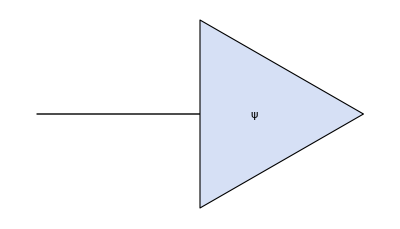

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{1,3}],ket["ψ",{3,0}]},ImageSize->{Automatic,25}]]
```

Matrices are rank-2 tensors, represented by an object with two legs

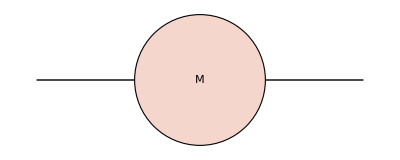

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-2,2}],opH["M",{0,0}]},ImageSize->{Automatic,25}]]
```

Tensor contraction: indices on internal legs are automatically summed over. For example, matrix-vector multiplication can be expressed as a tensor contraction.

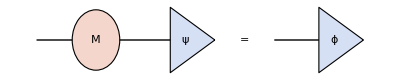

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-2,3}],opH["M"],ket["ψ",{3,0}],Line[{#,0}&/@{6,8}],ket["ϕ",{8,0}],Text["=",{5,0}]},ImageSize->{Automatic,30}]]
```

On an orthonormal basis, the matrix elements of an operator M can be extracted by

M_ij=iMj,

because the following identity holds

M=∑_ij iiMjj,

given that ∑_i ii=𝟙 is an identity operator. This trick is commonly used to find representations of states and operators, and is called the resolution of identity. See also Eq. (DisplayFormulaNumbered).

Composition of operators: one operation following by another (from right to left)

L M=∑_ij i L_ij j∑_kl k M_kl l
=∑_ij i(∑_k L_ik M_kj)j.

Composing two operators ≏ multiplying two matrices.

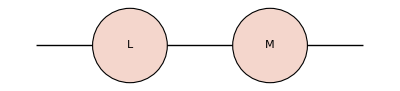

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-5,2}],opH["L",{-3,0}],opH["M",{0,0}]},ImageSize->{Automatic,25}]]
```

#### Hermitian Conjugate

We have talked about how an operator acts on a ket-vector ψ, what about its action on the bra-vector ψ?

Hilbert space | ⇒ | dual Hilbert space
ket–state ψ | ⇒ | bra–stateψ
operator M | ⇒ | Hermitian conjutate operator M^†

If Mψ=ϕ then ψ M^†=ϕ (which defines M^† as a dual/conjugate of M).

In terms of tensor networks, this corresponds to flipping tensors around.

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-2,3}],opH["M"],ket["ψ",{3,0}],Line[{#,0}&/@{6,8}],ket["ϕ",{8,0}],Text["=",{5,0}]},ImageSize->{Automatic,30}]]
```

-Graphics-

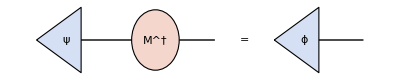

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{2,-3}],opH["M\^†"],bra["ψ",{-3,0}],Line[{#,0}&/@{5,7}],bra["ϕ",{5,0}],Text["=",{3,0}]},ImageSize->{Automatic,30}]]
```

Recall from Eq. (DisplayFormulaNumbered):

ψ=∑_i ψ_i i≏(ψ_1
ψ_2
⋮)
⇒ψ=∑_i i ψ_i^*≏(ψ_1^* | ψ_2^* | ⋯),

the way to get ψ M^†=ϕ is to define

M=∑_ij i M_ij j≏(M_11 | M_12 | ⋯
M_21 | M_22 | ⋯
⋮ | ⋮ | ⋱)
⇒M^†=∑_ij i M_ji^*j≏(M_11^* | M_21^* | ⋯
M_12^* | M_22^* | ⋯
⋮ | ⋮ | ⋱),

such that

ψ M^†=∑_i i ψ_i^*∑_jk j M_kj^*k
=∑_k ϕ_k^*k=ϕ.

where Eq. (DisplayFormulaNumbered) was used in the form of

ϕ_k^*=∑_j M_kj^*ψ_j^*,
(ϕ_1^* | ϕ_2^* | ⋯)=(ψ_1^* | ψ_2^* | ⋯)(M_11^* | M_21^* | ⋯
M_12^* | M_22^* | ⋯
⋮ | ⋮ | ⋱).

In terms of matrix representation, Hermitian conjugate acts as

matrix transpose (interchanges the rows and columns),

followed by complex conjugation of each matrix element.

How to think of it: Hermitian conjugate ∼ a generalization of complex conjugate from complex numbers to matrices.

Hermitian conjugate has the following properties:

Duality: suppose A is an operator

(A^†)^†=A.

Linearity: suppose A and B are operators, a and b are complex numbers,

(a A+b B)^†=a^*A^†+b^*B^†.

Factor reversal: suppose A and B are operators

(A B)^†=B^†A^†.

#### Hermitian Operator

Real numbers play a special role in physics. The results of any measurements are real. If in quantum mechanics, physical observables are represented by operators, how do we impose the “reality” condition on operators?

A real number is a number whose complex conjugation is itself.

A real operator Hermitian operator is an linear operator whose Hermitian conjugate is itself.

For example, if L=∑_ij i L_ij j is Hermitian, then

L=L^†,

or in terms of matrix elements,

L_ij=L_ji^*.

Given a complex number z, real part: Re z=(z+z^*)/2, imaginary part: Im z=(z-z^*)/(2ⅈ). Similarity, given a linear operator M

Re M=1/2(M+M^†), Im M=1/(2ⅈ)(M-M^†).

Both Re M and Im M are Hermitian operators.

#### Eigenvalues and Eigenvectors

In general, a linear operator acting on a state will change the state. But for a fixed linear operator M, there can be special states μ that remain the same under the operation. The only effect of M on these states is to rescale them by an overall factor μ (can be complex).

Mμ=μμ.

the μ (outside the ket) is a number, indicating how much the vector is rescaled under the action of M. This number is an eigenvalue of the operator.

μ is an eigenvector that is associated with its eigenvalue μ.

Given the matrix representation of an operator, its eigenvalues and eigenvectors can be found by solving the eigen equation by Mathematica.

```mathematica
Eigensystem[{{0,-1},{1,0}}]
```

{{ⅈ,-ⅈ},{{ⅈ,1},{-ⅈ,1}}}

For bra vectors,

Mμ=μμ⇒μ M^†=μμ^*.

What is special about Hermitian operators?

Eigenvalues of a Hermitian operator are real.

Eigenvectors of a Hermitian operator for a complete set of basis. (Any vector  can be expanded as a sum of these eigenvectors.)

If λ_1≠λ_2 are two unequal eigenvalues of a Hermitian operator, then their corresponding eigenvectors λ_1 and λ_2 are orthogonal (automatically).

Eigenvectors of the same eigenvalue can be made orthogonal (by orthogonalization, e.g. Gram-Schmidt procedure).

```mathematica
Orthogonalize[{{1,2},{3,4}}]
```

{{1/(√5),2/(√5)},{2/(√5),-1/(√5)}}

For bounded Hermitian operators (e.g. finite matrices in finite dimensional Hilbert space), eigenvectors can be normalized.

In conclusion, each Hermitian operator generates a set of complete and orthonormal basis for Hilbert space. The set of basis is also called the eigenbasis of a Hermitian operator.

Suppose L is Hermitian (L=L^†) and

Lλ_1=λ_1 λ_1,
Lλ_2=λ_2 λ_2.

We can flip the first equation λ_1 L^†=λ_1L=λ_1 λ_1^*,

λ_1Lλ_2=λ_1^*λ_1λ_2,
λ_1Lλ_2=λ_2 λ_1λ_2.

If λ_1=λ_2 (automatically implying λ_1=λ_2), Eq. (DisplayFormulaNumbered) implies λLλ=λ^*λλ=λλλ, so λ is real.

If λ_1 and λ_2 are two different (non-colinear) states,

with unequal eigenvalues λ_1≠λ_2, Eq. (DisplayFormulaNumbered) implies (λ_1-λ_2)λ_1λ_2=0, so λ_1λ_2=0.

but their eigenvalues λ_1=λ_2=λ happen to be the same. In this case, λ_1 and λ_2 are degenerate. Degenerated states span a subspace, called the degenerate subspace. Any state in the degenerate subspace

λ=z_1 λ_1+z_2 λ_2,

is an eigenvector of the Hermitian operator with the same eigenvalue λ, because

Lλ=z_1 Lλ_1+z_2 Lλ_2
=z_1 λλ_1+z_2 λλ_2
=λ(z_1 λ_1+z_2 λ_2)
=λλ.

Hermitian operators admits the following spectral decomposition in its own eigenbasis,

L=∑_i λ_i λ_i λ_i.

Note: unlike a generic matrix representation L=∑_ij i l_ij j, in the eigenbasis, the summation only run through the dimension of the Hilbert space once.

In the eigenbasis, the Hermitian operator is represented as a diagonal matrix. So the procedure of bring the matrix representation to its diagonal form by transforming to its eigenbasis is called diagonalization. (We will discuss more about it later.)

#### Measurement Postulate

Now we are well prepared to come back to Axiom 2.

Axiom 2 (Observables): Physical observables of a quantum system are described by Hermitian operators (represented by Hermitian matrices) acting on the associated Hilbert space.

Suppose we have a physical observable described the Hermitian operator L. It has a set of eigenvalues and eigenvectors

L=∑_i λ_i λ_i λ_i.

The possible outcomes of a measurement are the eigenvalues λ_i. (Assuming they are not degenerate for now.)

The measurement projects (collapses) the quantum state to the eigenstate λ_i that corresponds to the measurement outcome λ_i.

Now comes another axiom of quantum mechanics

Axiom 3 (Measurement): Given a quantum system in the state ψ and the observable L to be measured, the probability to observe the measurement outcome λ_i is p(λ_i)=(|λ_iψ|)^2.

No way to tell for certain which outcome will be observed. There is only a probability p(λ_i).

Probability is given by the square of the overlap. Why the square? Probability must be (i) real and positive, (ii) "gauge invariant" (i.e. independent of the overall phase of either states).

Subsequent measurement must confirm the result. ⇒ After the initial measurement, the state must have been collapsed to the eigenstate λ_i (but how?).

What if there is a degenerate subspace corresponding to the eigen value λ?

Projection operator of the eigenspace associated to λ

P(λ)=∑_λ_i λ_iδ(λ_i-λ)λ_i,
δ(λ_i-λ)=Piecewise[{{1, λ_i=λ,}, {0, λ_i≠λ.}}]

The probability to observe the measurement outcome λ will be

p(λ)=ψP(λ)ψ.

If the outcome λ is observed, the state must have collapsed to

ψ⟶^(measure L, get λ)(P(λ)ψ)/(ψP(λ)ψ^(1/2)).

Expectation value of the observable. The averaged measurement outcome over many repeated experiments (initial state must be prepared each time). By definition and use p(λ_i)=(|λ_iψ|)^2

⟨L⟩=∑_i λ_i p(λ_i)=∑_i ψλ_i λ_i λ_iψ,

given L=∑_i λ_i λ_i λ_i we have

⟨L⟩=ψLψ.

The answer is a real scalar (as L is Hermitian).

Represented as vectors and matrices,

(ψ_1^* | ψ_2^* | ⋯)(L_11 | L_12 | ⋯
L_21 | L_22 | ⋯
⋮ | ⋮ | ⋱)(ψ_1
ψ_2
⋮),

or in terms of tensor network,

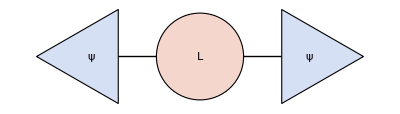

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-2,2}],opH["L"],bra["ψ",{-2,0}],ket["ψ",{2,0}]},ImageSize->{Automatic,25}]]
```

#### Example: Single-Qubit Operators

For a single qubit (spin), the physical observables are σ=(σ^x,σ^y,σ^z).

Each observable corresponds to a Hermitian operator acting in the 2-dimensional Hilbert space.

In the ↑ and ↓ basis, their matrix representations are

σ^x≏(0 | 1
1 | 0),
σ^y≏(0 | -ⅈ
ⅈ | 0),
σ^z≏(1 | 0
0 | -1).

These matrices are called Pauli matrices.

They are all Hermitian matrices.

Their eigenvectors are given by Eq. (DisplayFormulaNumbered), Eq. (DisplayFormulaNumbered), and Eq. (DisplayFormulaNumbered)

σ^x=+1≏1/(√2)(1
1), σ^x=-1≏1/(√2)(1
-1);
σ^y=+1≏1/(√2)(1
ⅈ), σ^y=-1≏1/(√2)(1
-ⅈ);
σ^z=+1≏(1
0), σ^z=-1≏(0
1).

Each set of eigenvectors form a set of complete and orthonormal basis of the qubit Hilbert space.

Their corresponding eigenvalues are all ±1: no matter we measure the qubit along x, y, z directions, we only get to possible outcomes ±1.

Let m and n be three-component real unit vectors. Define the operator m·σ=m_x σ^x+m_y σ^y+m_z σ^z for the vector m=(m_x,m_y,m_z), similarly for n.
(i) Write down the matrix representation of m·σ in the {↑,↓} basis.
(ii) If we measure the observable m·σ, what could be the possible measurement outcomes?
(iii) Show that the probability of observing n·σ=+1 when measuring the observable n·σ on the state m·σ=+1 is 1/2(1+m·n).
(iv) What is the expectation value of the operator n·σ on the state m·σ=+1? (in terms of m and n)

#### Measurement and Operator

We have learnt about:

observables are described by Hermitian operators,

measuring an observable on a quantum state could change the state (up on obtaining the outcome).

Is the change of state under the measurement implemented by the Hermitian operator? - No!

Example: prepare the qubit in ↑, measure σ^x ⇒ get ← or ← with probability 1/2 to 1/2. But σ^x operator does not take ↑ to either ← or ←. In fact σ^x↑=↓.

So what does the Hermitian operator really implement?

Hermitian operator attaches measurement outcomes (eigenvalues) to its eigenstates (as prefactors).

L=∑_i λ_i λ_i λ_i.

Example: suppose we measure σ^x and obtain:

σ^x=Piecewise[{{+1, →,}, {-1, ←,}}]

then the operator σ^x attaches the measurement outcome to the state

σ^x→=(+1)→=→,
σ^x←=(-1)←=-←.

What if we apply σ^x to ↑?

σ^x↑=σ^x 1/(√2)(→+←)
=1/(√2)(σ^x→+σ^x←)
=1/(√2)(→-←)
=↓.

As an operator, σ^x flips the spin (exchanges σ^z=±1 states).

As an observable, ψ σ^x ψ provides the expectation value of σ^x on any given state ψ (by the mechanism of attaching measurement outcomes).

Although measuring σ^x on ↑ ⇒ collapse ↑ to either ← or ←, this “collapse” operation is not implemented by the operator σ^x but by the projection operators (following a normalization procedure)

P_(σ^x=±1)=δ(σ^x=±1)=(𝟙±σ^x)/2.

In general, a Hermitian operator L can be used to define a family of projection operators (parameterized by λ)

P_L(λ)=δ(L-λ),

meaning

L=∑_i λ_i λ_i λ_i⇒P_L(λ)=∑_i λ_iδ(λ_i-λ)λ_i.

Quantum state collapse is implemented as

ψ⟶^(measure L, get λ)(P_L(λ)ψ)/(ψP_L(λ)ψ^(1/2)).

This is a non-linear operation on ψ ⇒ beyond the current framework of quantum mechanics (which only involves linear operators).

### Unitary Operators

#### Basis Transformation

What operator should we apply to rotate one basis to another?

Example:

U=↑→-↓←.

U maps → to |↑⟩ and maps ← to -↓.

Using explicit vector representations

↑≏(1
0), ↓≏(0
1);
→≏1/(√2)(1
1),←≏1/(√2)(1
-1).

we find

U≏1/(√2)(1 | 1
-1 | 1).

U is an example of unitary operator.

It implements a basis rotation, as if we have redefined σ^x to σ^z. Every state in the Hilbert space will rotate correspondingly.

U(z_1→+z_2←)=z_1↑-z_2↓.

A unitary operator is a linear operator whose Hermitian conjugation is its inverse, i.e.

U^†U=U U^†=𝟙.

Two operators are inverse to each other ⇔ sequential application of them is equivalent to applying the identity (do-nothing) operator 𝟙.

The operation implemented by U is countered by that of U^†, and vice versa.

Unitary operators implements basis rotation (mapping λ_i to μ_i).

U=∑_i λ_iμ_i,

If λ_i and μ_i are identical, U=𝟙 becomes the identity operator (which is also unitary).

One can verify that

U^†U=∑_i μ_iλ_i∑_j λ_jμ_j
=∑_ij μ_iλ_iλ_jμ_j
=∑_ij μ_i δ_ij μ_j
=∑_i μ_iμ_i=𝟙,

and similar for U U^†=𝟙. This means actually any basis transformation can be considered as a unitary operator.

Applying basis transformations to

ket states: | ψ→Uψ,
bra states: | ψ→ψ U^†,
operators: | L→U L U^†.

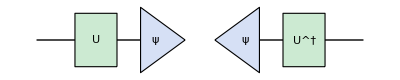

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-4,0}],ket["ψ"],opU["U",{-2,0}],Line[{#,0}&/@{3,7}],bra["ψ",{3,0}],opU["U\^†",{5,0}]},ImageSize->{Automatic,30}]]
```

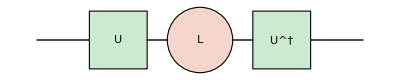

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-4,4}],opH["L"],opU["U",{-2,0}],opU["U\^†",{2,0}]},ImageSize->{Automatic,30}]]
```

Operator is made of ket and bra states, so the unitary operator must be applied from both sides.

The expectation value of an observable is invariant under basis transformation. (Measurement outcome should be basis-independent.)

⟨L⟩=ψLψ→ψ U^† U L U^†Uψ=ψ𝟙 L 𝟙ψ=⟨L⟩.

Diagonalization of a Hermitian operator: find a unitary operator to bring the Hermitian operator to diagonal form by transforming to its eigenbasis.

U=∑_i iλ_i,
L=∑_i λ_i λ_i λ_i,

such that under L→U L U^†,

Λ=U L U^†=∑_i i λ_i i≏(λ_1 | 0 | ⋯
0 | λ_2 | ⋯
⋮ | ⋮ | ⋱)

is diagonal.

Every Hermitian matrix can be written as

L=U^†Λ U,

where Λ is diagonal and U is unitary.

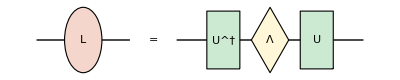

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-2,2}],opH["L"],Line[{#,0}&/@{4,12}],opU["U\^†",{6,0}],opD["Λ",{8,0}],opU["U",{10,0}],Text["=",{3,0}]},ImageSize->{Automatic,30}]]
```

Or equivalently, the unitary transformation U brings the Hermitian matrix to its diagonal form,

U L U^†=Λ.

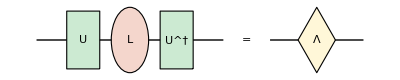

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-4,4}],opH["L"],opU["U",{-2,0}],opU["U\^†",{2,0}],Line[{#,0}&/@{6,10}],opD["Λ",{8,0}],Text["=",{5,0}]},ImageSize->{Automatic,30}]]
```

#### Hermitian Generators

If Hermitian operators are generalization of real numbers, then unitary operators are generalization of phase factors. (u∈ℂ and |u|=1)

u^*u=u u^*=(|u|)^2=1.

For complex numbers, a phase factor can be written as u=e^(ⅈ θ), where θ∈ℝ is a real phase angle.

Similar ideas apply to unitary operators: every unitary operator can be generated by a Hermitian operator in the form of

U=e^(ⅈ L).

Given a Hermitian operator L, by e^(ⅈ L) we mean

in the eigen basis

e^(ⅈ L)=∑_i λ_i e^(ⅈ λ_i)λ_i.

by operator Taylor expansion

e^(ⅈ L)=𝟙+ⅈ L+(ⅈ L)^2/(2!)+(ⅈ L)^3/(3!)+….

By definition, e^(ⅈ L) is unitary if L is Hermitian, since

U^†U=(e^(ⅈ L))^†e^(ⅈ L)=e^(-ⅈ L^†)e^(ⅈ L)=e^(-ⅈ L)e^(ⅈ L)=𝟙,

and similar for U U^†=𝟙.

For example, the unitary operator we encountered in Eq. (DisplayFormulaNumbered) can be generated by the Hermitian operator σ^y,

U≏1/(√2)(1 | 1
-1 | 1)=e^(π/4(0 | 1
-1 | 0))≏e^((ⅈ π)/4 σ^y).

```mathematica
MatrixExp[π/4{{0,1},{-1,0}}]
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

Another way to verify this is to switch to the eigenbasis as in Eq. (DisplayFormulaNumbered)

e^((ⅈ π)/4 σ_y)=⊗e^(+(ⅈ π)/4)⊗+⊙e^(-(ⅈ π)/4)⊙,

then using Eq. (DisplayFormulaNumbered) to show

e^((ⅈ π)/4 σ^y)≏1/2(1
ⅈ)e^(+(ⅈ π)/4)(1 | -ⅈ)+1/2(1
-ⅈ)e^(-(ⅈ π)/4)(1 | ⅈ)=1/(√2)(1 | 1
-1 | 1).

The coefficient π/4 in front of σ^y looks like an angle ⇒ let us try to replace it by an arbitrary angle θ:

e^(ⅈ θ σ^y)≏(cos θ | sin θ
-sin θ | cos θ)≏cos θ 𝟙+ⅈ sin θ σ^y.

```mathematica
MatrixExp[θ{{0,1},{-1,0}}]
```

{{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}

Let us verify it using Taylor expansion in Eq. (DisplayFormulaNumbered)

e^(ⅈ θ σ^y)=𝟙+ⅈ θ σ^y+1/(2!)(ⅈ θ σ^y)^2+1/(3!)(ⅈ θ σ^y)^3+1/(4!)(ⅈ θ σ^y)^4+…
=(1-1/(2!)θ^2+1/(4!)θ^4+…)𝟙+ⅈ (θ-1/(3!) θ^3+… )σ^y
=cos θ 𝟙+ⅈ sin θ σ^y.

Note that (σ^y)^2=𝟙. Consider U(θ)=e^(ⅈ θ σ^y). It implements a basis rotation with θ being the rotation angle:

U(θ)↑=cos θ ↑-sin θ ↓≏(cos θ
-sin θ).

Special case: when θ=0, U(0)=𝟙 ⇒ no rotation is performed.

More generally, let U(θ) be the unitary operator that implements certain basis rotation by an angle θ. When θ=Δθ is small, we can Taylor expand

U(Δθ)=U(0)+U'(0)Δθ+…=𝟙+U'(0)Δθ+…,

where U'(0) is ∂_θ U(θ) evaluated at θ=0.

U'(0) is also an operator (matrix), usually denoted as U'(0)=ⅈ L. We call L the generator of the rotation/unitary operator, because it generates an infinitesimal rotation

U(Δθ)=𝟙+ⅈ Δθ L+....

U(Δθ) is unitary ⇒ L is Hermitian.

(U(Δθ))^†U(Δθ)
=(𝟙-ⅈ Δθ L^†+...)(𝟙+ⅈ Δθ L+...)
=𝟙+ⅈ Δθ(L-L^†)+…=𝟙.

Large rotations can be accumulated from small rotations.

U(N Δθ)=(U(Δθ))^N=(𝟙+ⅈ Δθ L)^N.

As Δθ is small (but N can be large, s.t. θ=N Δθ is finite),

ln U(N Δθ)=N ln(𝟙+ⅈ Δθ L)=ⅈ N Δθ L,

So U(N Δθ)=e^(ⅈ N Δθ L), we obtain the exponential form

U(θ)=e^(ⅈ θ L).

Conclusion: every Hermitian operator generates a unitary operator.

#### Time-Evolution is Unitary

Unitarity: information is never lost.

Two identical and isolated systems, start out in different states ⇒ remains in different states (in both future and past).

Two identical and isolated systems, start out in the same state ⇒ follow identical evolution (in both future and past).

Although measurement seems to be non-deterministic, evolution of quantum state is deterministic: suppose you know the state at one time, then the quantum equation of motion tell you what it will be later.

ψ(t)=U(t)ψ(0),

ψ(0) is the initial state, and ψ(t) is the state at time t. U(t) is the time-evolution operator that takes ψ(0) to ψ(t). ☟We will show that U(t) should be unitary.

Different states remain different (here, different states are states that can be told apart definitely by a measurement, due to their different outcomes, so they are actually orthogonal):

ϕ(0)ψ(0)=0⇒ϕ(t)ψ(t)=ϕ(0)(U(t))^†U(t)ψ(0)=0.

Same states remain the same

ψ(0)ψ(0)=1⇒ψ(t)ψ(t)=ψ(0)(U(t))^†U(t)ψ(0)=1.

Or, the fact that the probability adds up to 1 is preserved.

Treat ψ(0) and ϕ(0) as members of any orthonormal basis, then Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) implies

i(U(t))^†U(t)j=δ_ij⇒(U(t))^†U(t)=𝟙.

Therefore, the time-evolution operator U(t) is unitary.

#### Hamiltonian and Schrödinger Equation

Hamiltonian generates time-evolution!

As a unitary operator, the time-evolution operator is also generated by a Hermitian operator, called the Hamiltonian,

H=ⅈ U'(0)=ⅈ ∂_t U(t)|_(t=0).

For small Δt, infinitesimal evolution is given by

U(Δt)=𝟙-ⅈ H Δt+...,

therefore the state evolves as

ψ(Δt)=U(Δt)ψ(0)=ψ(0)-ⅈ Δt Hψ(0),

meaning that

ⅈ ∂_t ψ(0)=ⅈ (ψ(Δt)-ψ(0))/Δt=Hψ(0).

There is nothing special about t=0. Eq. (DisplayFormulaNumbered) should hold at any time.

ⅈ∂_t ψ(t)=Hψ(t).

This is the Schrödinger equation, the equation of motion for the quantum state.

The Hamiltonian H(t)=ⅈ U'(t) can be time-dependent in general.

But in many cases, we consider H to be time-independent, by assuming the time-translation symmetry.

What happens to Planck’s constant?

ℏ=h/(2π)=1.0545718(13)×10^-34 J s.

In quantum mechanics, the observable associated with the Hamiltonian is the energy. To balance the dimensionality across the Schrödinger equation, Planck’s constant is inserted for Eq. (DisplayFormulaNumbered):

ⅈ ℏ∂_t ψ(t)=Hψ(t).

Why is ℏ so small? Well, the answer has more to do with biology than with physics ⇒ Why we are so big, heavy and slow? A natural choice for quantum mechanics is to set the units such that ℏ=1. It is a common practice in theoretical physics (we will also use this convention sometimes).

We conclude with another axiom of quantum mechanics

Axiom 4 (Dynamics): The time-evolution of the state of a quantum system is governed by the Hamiltonian of the system, according to the time-dependent Schrödinger equation.

ⅈ ℏ∂_t ψ(t)=Hψ(t).

If the Hamiltonian H is time-independent, we can first find its eigenvalues (eigenenergies) and eigenvectors (energy eigenstates).

HE_i=E_i E_i.

This is also called the time-independent Schrödinger equation. Without solving a differential equation, we just need to diagonalize a Hermitian matrix in this case.

Each energy eigenstate will evolve in time simply by a rotating overall phase,

E_i(t)=e^(-ⅈ/ℏ E_i t)E_i.

E_i form a complete set of orthonormal basis, called energy eigenbasis.

Verify that Eq. (DisplayFormulaNumbered) is a solution of Eq. (DisplayFormulaNumbered):

ⅈ ℏ∂_t E_i(t)=ⅈ ℏ∂_t (e^(-ⅈ/ℏ E_i t)E_i)=E_i E_i(t),
HE_i(t)=e^(-ⅈ/ℏ E_i t)HE_i=E_i E_i(t).

So the two sides matches.

Any initial state ψ(0) will evolve in time by first representing the initial state in the energy eigenbasis, and attaching to each energy eigenstate by its rotating overall phase,

ψ(t)=∑_i e^(-ⅈ/ℏ E_i t)E_iE_iψ(0)
=e^(-ⅈ/ℏ H t)ψ(0).

A time-independent Hamiltonian generates the time-evolution via matrix exponentiation

U(t)=e^(-ⅈ/ℏ H t).

However, for time-dependent Hamiltonian, there no such a clean formula. Evolution must be carried out step by step, denoted as a time-ordered exponential

U(t)=𝒯 exp(-ⅈ/ℏ∫_0^t H(t')ⅆ t').

#### Example: Spin in a Magnetic Field

How to write down a Hamiltonian?

derive it from experiment,

borrow it from some theory we like,

pick one and see what happens.☜

Hamiltonian must be Hermitian anyway. For a single qubit, the most general Hamiltonian takes the form of

H=h_0 𝟙+h_x σ^x+h_y σ^y+h_z σ^z
=h_0 𝟙+h·σ,

where h_0,h_x,h_y,h_z∈ℝ are all real coefficients. h=(h_x,h_y,h_z) is a vector of numbers and σ=(σ^x,σ^y,σ^z) is a vector of operators.

The time-evolution operator (set ℏ=1 in the following)

U(t)=e^(-ⅈ H t)
=e^(-ⅈ h_0 t)(cos(|h|t)𝟙-ⅈ sin(|h|t)ĥ·σ),

where |h|=√(h·h) and ĥ=h/|h|.

A state ψ(0) will evolve with time following

ψ(t)=U(t)ψ(0)
=e^(-ⅈ h_0 t)(cos(|h|t)𝟙-ⅈ sin(|h|t)ĥ·σ)ψ(0).

If we measure σ on the state ψ(t), the expectation value will be given by

⟨σ⟩_t=ψ(t)σψ(t)
=cos(2|h|t)⟨σ⟩_0+sin(2|h|t)ĥ×⟨σ⟩_0+(1-cos(2|h|t))ĥ(ĥ·⟨σ⟩_0).

which also evolves with time.

(i) Derive Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).
(ii) Derive Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).

Special case: assume h=(0,0,h_z) along the z-direction, and parameterize the expectation of the spin vector by ⟨σ⟩=(sin θ cos φ,sin θ sin φ,cos θ).

⟨σ⟩_t=(sin θ_0 cos (φ_0+2 h_z t), sin θ_0 sin(φ_0+2 h_z t),cos θ_0),

where θ_0 and φ_0 are the initial azimuthal and polar angles.

The spin should precess around the axis of the magnetic field ⇒ h has the physical meaning of the external magnetic field.

Energy of a spin in the magnetic field is ⟨H⟩=-h·⟨σ⟩ (up to some constant energy shift h_0).

### Operator Algebra

#### Commutator

Commutator of two operators A and B

[A,B]=A B-B A.

Commutator is antisymmetric, [A,B]=-[B,A]. As a result, commutator of an operator with itself always vanishes [A,A]=0.

If the commutator vanishes [A,B]=0, we say that the two operators A and B commute.

Example of commutators:

[σ^x,σ^y]=2ⅈ σ^z,
[σ^y,σ^z]=2ⅈ σ^x,
[σ^z,σ^x]=2ⅈ σ^y.

Or more compactly as

[σ^a,σ^b]=2ⅈ ϵ^abc σ^c,

for a,b,c=1,2,3 (stand for x,y,z). This can be considered as the defining algebraic properties of single-qubit operators (Pauli matrices). Or even more compactly using the cross product of vectors

σ×σ=2ⅈ σ.

Useful rules to evaluate commutators

Bilinearity

[A,B+C]=[A,B]+[A,C],
[A+B,C]=[A,C]+[B,C].

Product rules

[A,B C]=[A,B]C+B[A,C],
[A B,C]=[A,C]B+A[B,C].

Jacobi identity (as a replacement of associative law)

[A,[B,C]]+[B,[C,A]]+[C,[A,B]]=0,
[[A,B],C]+[[B,C],A]+[[C,A],B]=0.

#### Commutation Relation

A and B commute: A B=B A (operators can pass though each other as if they were numbers) ⇒ it does not matter which operator is applied first, the consequence will be the same.

Examples:

A: put on the socks,

B: put on the shoes,

C: put on the hat,

A and B do not commute (changing the order leads to different result). But A and C commute, B and C also commute (changing the order does not affect the result).

An operator always commutes with itself.

Identity operator commutes with any operator.

##### Commutation Relation (Single-Qubit)

For a generic qubit state ψ≏(ψ_↑
ψ_↓),

σ^z σ^x ψ:(ψ_↑
ψ_↓)→^(σ^x)(ψ_↓
ψ_↑)→^(σ^z)(ψ_↓
-ψ_↑),
σ^x σ^z ψ:(ψ_↑
ψ_↓)→^(σ^z)(ψ_↑
-ψ_↓)→^(σ^x)(-ψ_↓
ψ_↑).

Conclusion: σ^x and σ^z do not commute. In fact, [σ^z,σ^x]=2ⅈ σ^y≠0, which can be readily verified from their matrix representations

σ^z≏(1 | 0
0 | -1),σ^x≏(0 | 1
1 | 0).

↑ and ↓ are eigenstates of σ^z with different eigenvalues. σ^z marks the states differently, and σ^x mixes the states. In general, “markers” and “mixers” do not commute.

##### Commutation Relation (Two-Qubit)

Define σ^ab=σ^a⊗σ^b, e.g.

σ^12=σ^1⊗σ^2=(0 | 1
1 | 0)⊗(0 | -ⅈ
ⅈ | 0)=(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),
σ^23=σ^2⊗σ^3=(0 | -ⅈ
ⅈ | 0)⊗(1 | 0
0 | -1)=(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0).

Note: in general, tensor product of two matrices is given by

(A_11 | A_12
A_21 | A_22)⊗(B_11 | B_12
B_21 | B_22)
=(A_11(B_11 | B_12
B_21 | B_22) | A_12(B_11 | B_12
B_21 | B_22)
A_21(B_11 | B_12
B_21 | B_22) | A_22(B_11 | B_12
B_21 | B_22))
=(A_11 B_11 | A_11 B_12 | A_12 B_11 | A_12 B_12
A_11 B_21 | A_11 B_22 | A_12 B_21 | A_12 B_22
A_21 B_11 | A_21 B_12 | A_22 B_11 | A_22 B_12
A_21 B_21 | A_21 B_22 | A_22 B_21 | A_22 B_22).

You can use Mathematica to calculate tensor product like this:

```mathematica
MatrixForm@KroneckerProduct[PauliMatrix[1],PauliMatrix[2]]
```

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)

Consider two Hermitian operators A and B in this four dimensional Hilbert space:

A≏σ^12, B≏σ^23.

Do A and B commute?

Yes, because we can explicitly verify [σ^12,σ^23]=0 using the matrix representation.

```mathematica
A=KroneckerProduct[PauliMatrix[1],PauliMatrix[2]];
B=KroneckerProduct[PauliMatrix[2],PauliMatrix[3]];
A.B-B.A//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

But is there a better way to see this?

Switch to the diagonal basis of A: find a unitary operator (choice is not unique) to diagonalize A

U_1≏e^((ⅈ π)/4 σ^22)=1/(√2)(1 | 0 | 0 | -ⅈ
0 | 1 | ⅈ | 0
0 | ⅈ | 1 | 0
-ⅈ | 0 | 0 | 1).

U_1 takes A and B to the block diagonal form

A→A'=U_1 A U_1^†≏σ^30=(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),
B→B'=U_1 B U_1^†≏-σ^01=(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0).

```mathematica
A=KroneckerProduct[PauliMatrix[1],PauliMatrix[2]];
B=KroneckerProduct[PauliMatrix[2],PauliMatrix[3]];
U1=MatrixExp[ⅈ π/4 KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]];
MatrixForm[U1.#.ConjugateTranspose[U1]]&/@{A,B}
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)}

B' does not mix different eigenspaces of A' ⇒  A' and B' commute ⇒ A and B also commute.

Show that the fact that two operator commute (or not commute) is independent of the choice of basis, i.e. suppose A'=U A U^† and B'=U B U^†, then [A,B]=0 ⇔ [A',B']=0.

Mixing within the block (by B') does not cause a problem, why? Because A' look like an identity matrix within each block, which commutes with any matrix within the same block.

Diagonal blocks can be further diagonalized independently (within each block). For example, we can take

U_2≏e^((ⅈ π)/4 σ^02)=1/(√2)(1 | 1 | 0 | 0
-1 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | -1 | 1),

under which

A'→A'' =U_2 A' U_2^†≏σ^30=(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),
B'→B''=U_2 B' U_2^†≏σ^03=(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1).

The combined unitary transformation U=U_2 U_1 simultaneously diagonalize A and B, such that A''=U A U^† and B''=U B U^† are both diagonal.

##### Commutation Relation (General Discussions)

In fact, commuting operators can always be simultaneously diagonalized.

Suppose {A_1,A_2,…} is a set of commuting (Hermitian) operators, i.e. ∀i,j:[A_i,A_j]=0, the general algorithm to simultaneous diagonalize them is to first form a random Hamiltonian

H=∑_i r_i A_i,

with r_i being random real numbers. Find a unitary operator U to diagonalize the Hamiltonian H, the same unitary U would simultaneously diagonalize all A_i with probability 1.

```mathematica
As={KroneckerProduct[PauliMatrix[1],PauliMatrix[2]],KroneckerProduct[PauliMatrix[2],PauliMatrix[3]]};
MatrixForm/@As
```

{(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)}

```mathematica
H=RandomReal[{-1,1},Length@As].As;
MatrixForm@H
```

(0.+0. ⅈ | 0.+0. ⅈ | 0.-0.959637 ⅈ | 0.+0.678076 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.-0.678076 ⅈ | 0.+0.959637 ⅈ
0.+0.959637 ⅈ | 0.+0.678076 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.-0.678076 ⅈ | 0.-0.959637 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

```mathematica
U=Conjugate@Eigenvectors@H;
MatrixForm@Chop[U.#.ConjugateTranspose[U]]&/@As
```

{(-1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | -1.),(1. | 0 | 0 | 0
0 | -1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | -1.)}

Commuting operators can share a set of common eigenvectors, which can always be constructed by simultaneous diagonalization. For example, if [A,B]=0, there exist a set of vectors α,β,

Aα,β=αα,β,
Bα,β=βα,β.

Each eigenvector is labeled jointly by the eigenvalues α and β.

Commuting physical observables can be simultaneously measured.

The possible outcomes of a joint measurement of (A,B) are given by the pairs of eigenvalues (α,β).

On a given state ψ, the probability to obtain the measurement outcome (α,β) is given by

p(α,β)=(|α,βψ|)^2.

After the measurement, the state is projected to the common eigenstate α,β that corresponds to the measurement outcome (α,β).

Non-commuting physical observables do not share common eigenstates, therefore do not support a consistent joint measurement. The amount of inconsistency (uncertainty) of the joint measurement is characterized by the commutator. This statement is more precisely formulated as the uncertainty relation.

#### Uncertainty Relation

Statistics of measurement. Consider an observable L, whose eigenvalues are λ (i.e. Lλ=λλ), measured on a state ψ in repeated experiments (prepare ψ → measure L → repeat). Possible outcomes λ appear with probability p(λ)=(|λψ|)^2.

Mean (expectation value):

⟨L⟩=∑_λ λ p(λ)=ψLψ.

Variance (2nd moment):

varL=∑_λ (λ-⟨L⟩)^2 p(λ)=(ψ(L-⟨L⟩𝟙))^2 ψ.

Introduce the observable (the fluctuation of L around its expectation value)

ΔL=L-⟨L⟩𝟙,

The variance can be written as var L=⟨(ΔL)^2⟩.

Standard deviation: characterizes the uncertainty of the measurement of L

stdL=(varL)^(1/2)=⟨(ΔL)^2⟩^(1/2).

Uncertainty Relation: for any pair of observables A and B measured on any given state (repeatedly),

(std A)(std B)≥1/2|⟨[A,B]⟩|.

In words, the product of the uncertainties cannot be smaller than half of the magnitude of the expectation value of the commutator.

For commuting observables ([L,M]=0), (std L)(std M)≥0, it is possible to have std L=std M=0 simultaneously, i.e. L and M can be jointly measured with perfect certainty.

For non-commuting observables, if |⟨[L,M]⟩|≠0, it is impossible to have std L=std M=0 simultaneously, i.e. L and M can not be jointly measured with certainty.

Proof of the uncertainty relation:

Suppose A and B are Hermitian operators. Let ϕ=(A+ⅈ x B)ψ. For any choice of x∈ℝ,

ψ(A-ⅈ x B)(A+ⅈ x B)ψ=ϕϕ≥0.

On the other hand,

ψ(A-ⅈ x B)(A+ⅈ x B)ψ
=ψ A^2+ⅈ x [A,B]+x^2 B^2 ψ
=⟨B^2⟩x^2+ⅈ⟨[A,B]⟩x+⟨A^2⟩≥0,

where ⟨*⟩ is a shorthand notation of ψ*ψ. The quadratic equation ⟨B^2⟩x^2+ⅈ⟨[A,B]⟩x+⟨A^2⟩=0 has no (or only one) real root, implying that its discriminant Δ must be negative (or zero), i.e.

Δ=(ⅈ⟨[A,B]⟩)^2-4⟨B^2⟩⟨A^2⟩≤0.

Therefore for any A,B on any state ψ,

⟨A^2⟩^(1/2)⟨B^2⟩^(1/2)≥1/2|⟨[A,B]⟩|.

The uncertainty relation Eq. (DisplayFormulaNumbered) can be shown by replacing A→ΔA and B→ΔB.

Suppose A and B are Hermitian operators.
(i) Show that ⟨A^2⟩,  ⟨B^2⟩ and  ⅈ⟨[A,B]⟩ are real.
(ii) Show that [ΔA,ΔB]=[A,B].

#### Operator Dynamics

Two pictures of the quantum dynamics:

Schrödinger picture: state evolves in time, operator remains fixed,

⟨L(t)⟩=ψ(t)Lψ(t).

Heisenberg picture: operator evolves in time, state remains fixed,

⟨L(t)⟩=ψL(t)ψ.

The two pictures are consistent, if

ψ(t)=U(t)ψ⇒L(t)=(U(t))^†L U(t),

such that Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) are consistent, as they both implies

⟨L(t)⟩=ψ(U(t))^†L U(t)ψ.

Note: one should only apply one picture at a time, i.e. either the state or the operator is time-dependent, but not both.

In the Heisenberg picture, the time-evolution of an operator

L(t)=U(t)^†L U(t),

described by the Heisenberg equation

ⅈ ℏ∂_t L(t)=[L(t),H].

A sketch of the derivation: for small Δt (with ℏ=1)

L(Δt)=(U(Δt))^†L U(Δt)
=e^(ⅈ H Δt)L e^(-ⅈ H Δt)
=(𝟙+ⅈ H Δt+…)L (𝟙-ⅈ H Δt+…)
=L+ⅈ (H L-L H) Δt+…
=L-ⅈ [L,H] Δt+…

therefore

ⅈ ∂_t L=ⅈ(L(Δt)-L)/Δt=[L,H].

Correspondingly, its expectation value evolves as

ⅈ ℏ∂_t ⟨L(t)⟩=⟨[L(t),H]⟩.

If [L,H]=0, the Heisenberg equation Eq. (DisplayFormulaNumbered) implies that ∂_t L=0, i.e. L will be invariant in time. The observable L is a conserved quantity (or an integral of motion) if L commutes with the Hamiltonian H.

Consider a single-qubit Hamiltonian H=h·S, where S=ℏ/2 σ is the spin operator.
(i) Show that the expectation values of the spin operator evolves as ∂_t ⟨S⟩=h×⟨S⟩.
(ii) Show that
⟨S(t)⟩=cos(|h|t)⟨S(0)⟩+sin(|h|t)ĥ×⟨S(0)⟩+(1-cos(|h|t))ĥ(ĥ·⟨S(0)⟩)
is a solution of ∂_t ⟨S⟩=h×⟨S⟩, where ĥ=h/|h|.
This describes the dynamics of a spin in a magnetic field h.
(iii) Show that the spin component along the magnetic field ĥ·S is a conserved quantity, that generates the SO(2) symmetry of the Hamiltonian.

### Density Matrix

#### Idea of Density Matrix

Motivation: an alternative way to think about the expectation value of an observable L

⟨L⟩=ψLψ=TrψψL.

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{{EdgeForm[Directive[AbsoluteThickness[1],Dashed]],Lighter[Blue,0.9],Rectangle[{5.5,-1.2},{9.5,1.2},RoundingRadius->.3]},Line[{#,0}&/@{-2,2}],opH["L"],bra["ψ",{-2,0}],ket["ψ",{2,0}],Text["=",{4,0}],BSplineCurve[{{6,0},{6,0},{6,0},{5,0},{5,1.5},{6,1.5},{11,1.5},{12,1.5},{12,0},{11,0},{9,0},{9,0},{9,0}}],ket["ψ",{6.3,0}],bra["ψ",{8.7,0}],opH["L",{10.5,0}],Text["ρ",{7.5,-0.8}]},ImageSize->{Automatic,45}]]
```

-Graphics-

Introduce the density matrix (density operator) of a quantum state ψ

ρ=ψψ,

as an equivalent description of the state.

The normalization of the state ψψ=1 implies the normalization of the density matrix

Tr ρ=1.

The expectation value of an physical observable L measured with respect to the state ρ is given by

⟨L⟩=Tr ρ L.

Example: density matrix of a qubit. Assume a qubit describe by the following state

ψ=ψ_↑↑+ψ_↓↓≏(ψ_↑
ψ_↓).

Density matrix can be constructed as

ρ=ψψ≏(ψ_↑
ψ_↓)(ψ_↑^* | ψ_↓^*)=((|ψ_↑|)^2 | ψ_↑ψ_↓^*
ψ_↓ψ_↑^* | (|ψ_↓|)^2).

Evaluate expectation values of qubit operators using density matrix

⟨σ^x⟩=Tr ρ σ^x≏Tr((|ψ_↑|)^2 | ψ_↑ψ_↓^*
ψ_↓ψ_↑^* | (|ψ_↓|)^2)(0 | 1
1 | 0)=ψ_↑^*ψ_↓+ψ_↓^*ψ_↑,
⟨σ^y⟩=Tr ρ σ^y≏Tr((|ψ_↑|)^2 | ψ_↑ψ_↓^*
ψ_↓ψ_↑^* | (|ψ_↓|)^2)(0 | -ⅈ
ⅈ | 0)=-ⅈ ψ_↑^*ψ_↓+ⅈ ψ_↓^*ψ_↑,
⟨σ^z⟩=Tr ρ σ^z≏Tr((|ψ_↑|)^2 | ψ_↑ψ_↓^*
ψ_↓ψ_↑^* | (|ψ_↓|)^2)(1 | 0
0 | -1)=(|ψ_↑|)^2-(|ψ_↓|)^2.

What if there is a 50% possibility that the system is prepared in ψ and 50% probability in ϕ? The expectation value of an observable L should be

⟨L⟩=1/2 ψ Lψ+1/2 ϕ Lϕ
=1/2 Tr ψψ L+1/2 Tr ϕϕ L
=Tr(1/2 ψψ+1/2 ϕϕ)L.

We are just averaging over our ignorance of the state preparation. Now we can define a density matrix to describe our knowledge about the system

ρ=1/2 ψψ+1/2 ϕϕ,

such that the rule to compute expectation value is still ⟨L⟩=Tr ρ L as in Eq. (DisplayFormulaNumbered).

In general, the density matrix is defined for an ensemble of quantum systems, other than a single quantum system.

Suppose the system is randomly prepared in the state ϕ_i with probability p_i, the density matrix of the ensemble is given by

ρ=∑_i ϕ_i p_i ϕ_i.

A density matrix should satisfy the following properties

Hermitian: ρ^†=ρ.

Normalization (trace one): Tr ρ=1.

Positive (semi)definite: ∀ψ:ψρψ≥0.

Not every density matrix can be expressed in the form of ψψ ⇒ A density matrix is richer and more general than a state vector.

Quantum Tomography: reconstruction of the density matrix from (repeated) measurements on the systems taken from the ensemble. For a single qubit, by measuring ⟨σ⟩, the density matrix can be reconstructed as

ρ=1/2(𝟙+⟨σ⟩·σ).

As ρ is the only solution of the density matrix that is normalized and reproduces the expectation values of all measurements on the qubit.

Check that the density matrix ρ in Eq. (DisplayFormulaNumbered) is normalized Tr ρ=1 and reproduces all measurement expectation values Tr ρ σ=⟨σ⟩.

#### Dynamics of Density Matrix

The time-evolution of the density matrix follows the von Neumann equation (also known as the Liouville-von Neumann equation)

ⅈ ℏ∂_t ρ(t)=[H,ρ(t)].

Here the density matrix is taken to be in the Schrödinger picture.

Even though the von Neumann equation looks like the Heisenberg equation ⅈ ℏ∂_t L(t)=-[H,L(t)] (which governs the operator evolution in the Heisenberg picture), but there is a crucial sign difference.

However in the Heisenberg picture, the density matrix is time-independent, because the state does not evolve in the Heisenberg picture and the density matrix follows the state.

In the case of ρ(t)=ψ(t)ψ(t), derive the von Neumann equation Eq. (DisplayFormulaNumbered) from the Schrödinger equation Eq. (DisplayFormulaNumbered).

If the time-evolution of the state is described by the unitary operator U(t), the density matrix evolves as

ρ(t)=U(t)ρ(0)(U(t))^†.

Example: Consider a single-qubit Hamiltonian H=ω/2 σ^z. Starting from the initial density matrix (in the diagonal basis of H)

ρ(0)≏((|ψ_↑|)^2 | ψ_↑ψ_↓^*
ψ_↓ψ_↑^* | (|ψ_↓|)^2).

Under time evolution (set ℏ=1),

ρ(t)≏((|ψ_↑|)^2 | ψ_↑ψ_↓^*e^(-ⅈ ω t)
ψ_↓ψ_↑^*e^(ⅈ ω t) | (|ψ_↓|)^2).

The diagonal elements are invariant, the off-diagonal elements rotates in time following e^(±ⅈ ω t) (with an angular frequency of ω).

#### Measurement and Decoherence

Measurement Postulate in terms of density matrix

An ensemble of quantum states is described by a density matrix ρ.

A physical observable is described by a Hermitian operator L=∑_i λ_i λ_i λ_i.

Define the projection operator P_L(λ), which projects to the eigenspace of L of the eigenvalue λ (it is also fine if λ is not an eigenvalue of L, P_L(λ) will then project out all states),

P_L(λ)=∑_i λ_iδ(λ-λ_i)λ_i=δ(λ-L).

The probability to observe the measurement outcome λ by measuring L on ρ is given by

p(λ)=Tr ρ P_L(λ).

The expectation value of the observable L is given by

⟨L⟩=Tr ρ L.

The ensemble post-selected upon the observation of outcome λ is described by

ρ ⟶^(measure L, get λ)(P_L(λ)ρ P_L(λ))/(p(λ)).

Measurement couples the quantum system to the apparatus (and eventually the entire environment). In the view of the system, suppose the coupling is resembled a relative energy shift between ↑ and ↓ states, i.e. H=ω/2 σ^z. The density matrix evolves as Eq. (DisplayFormulaNumbered),

ρ(t)≏((|ψ_↑|)^2 | ψ_↑ψ_↓^*e^(-ⅈ ω t)
ψ_↓ψ_↑^*e^(ⅈ ω t) | (|ψ_↓|)^2).

If ω is large (the coupling is strong) and noisy (the environment is chaotic), e^(±ⅈ ω t) looks like a fast fluctuating random phase, which averages to zero over a short period of time.

ρ̄=1/T∫_0^∞ ρ(t)e^(-t/T)ⅆt
≏((|ψ_↑|)^2 | (ψ_↑ψ_↓^*)/(1+ⅈ ω T)
(ψ_↓ψ_↑^*)/(1-ⅈ ω T) | (|ψ_↓|)^2) ⟶^(ωT≫1)((|ψ_↑|)^2 | 0
0 | (|ψ_↓|)^2).

The off-diagonal elements of the density matrix decays much more quickly than the diagonal elements, due to its fast oscillating phase (in this model). (We will come back later with a better model.)

Quantum Decoherence (brief idea): the loss of off-diagonal density matrix elements (quantum coherence) over time in the measurement basis determined by how the system is coupled to the apparatus.

After quantum decoherence, the time-averaged density matrix

ρ̄=↑(|ψ_↑|)^2↑+↓(|ψ_↓|)^2↓

describes a qubit ensemble with

probability | to be in the sate
(|ψ_↑|)^2 | ↑,
(|ψ_↓|)^2 | ↓.

Note: quantum decoherence dose not generate actual quantum state collapse. It only provides an ensemble of quantum states that matches the measurement postulate. The measurement problem “How the measurement actually leads to the realization of precisely one state in the ensemble?” remains an issue of interpretation.

#### Pure State and Mixed State

Pure state: a coherent quantum state, described by a state vector ψ, or a pure state density matrix of the form ρ=ψψ.

Mixed state: a statistical mixture of pure states, can not be described by any single state vector, described by a mixed state density matrix as a superposition of pure state density matrices.

Superposition at different levels:

Quantum superposition (pure state superposition): superposition of state vectors

ψ=z_1 ϕ_1+z_2 ϕ_2+….

The result is still a pure state.

Statistical superposition (mixed state superposition): superposition of density matrices

ρ=p_1 ϕ_1ϕ_1+p_2 ϕ_2ϕ_2+…,

or more generally, ρ=p_1 ρ_1+p_2 ρ_2+…. The result is generally a mixed state.

In terms of the density matrix, a quantum superposition of Eq. (DisplayFormulaNumbered) is expressed as

ψψ=(|z_1|)^2 ϕ_1ϕ_1+(|z_2|)^2 ϕ_2ϕ_2+
+z_1 z_2^*ϕ_1ϕ_2+z_2 z_1^*ϕ_2ϕ_1+…,

also involves cross terms that represents quantum coherence.

Spectral decomposition of the density matrix

ρ=∑_i p_i ϕ_iϕ_i.

As ρ is Hermitian, its eigenvectors ϕ_i form an orthonormal basis.

The eigenvalues p_i has the physical meaning of probability, with the following properties:

Hermitian: ρ^†=ρ ⇔ p_i∈ℝ.

Normalization (trace one): Tr ρ=1 ⇔ ∑_i p_i=1.

Positive (semi)definite: ∀ψ:ψρψ≥0 ⇔ p_i≥0.

The density matrix ρ describes an ensemble of quantum systems, where each pure state ϕ_i is prepared with probability p_i.

If p_i have only a single one followed by all zeros, e.g. p_1=1, p_2=p_3=…=0, the density matrix ρ is pure, since it can be written as ρ=ϕ_1ϕ_1.

Otherwise, for generic distribution of p_i, the density matrix ρ is mixed.

Purity: to quantify to which degree the density matrix is pure/mixed,

Tr ρ^2=∑_i p_i^2

By construction, Tr ρ^2∈[0,1]. The criteria to determine if a density matrix ρ is pure or mixed is

ρ is Piecewise[{{pure, if Tr ρ^2=1,}, {mixed, if Tr ρ^2<1.}}]

(i) Show that for a single qubit, the purity is related to the spin expectation value ⟨σ⟩=Tr ρ σ by Tr ρ^2=(1+⟨σ⟩^2)/2. 
(ii) For pure state, what is the norm of the spin expectation value |⟨σ⟩|?
(iii) What is the minimal possible purity of a qubit? When the minimal purity is achieved (the qubit is maximally mixed) what is the spin expectation value ⟨σ⟩?

#### von Neumann and Rényi Entropy

von Neumann entropy of a density matrix

S^(1)=-Tr ρ ln ρ.

In terms of the eigenvalues p_i, S^(1)=-∑_i p_i ln p_i matches the Shannon entropy of a probability distribution in the information theory.

Rényi entropy of a density matrix

S^(n)=1/(1-n)ln Tr ρ^n.

In terms of the eigenvalues p_i, S^(n)=(1-n)^-1 ln ∑_i p_i^n.

n is the Rényi index.

n=0: max-entropy, simply counts the log of the Hilbert space dimension S^(0)=ln dim ℋ.

n→1 limit: equivalent to the von Neumann entropy, i.e. S^(1)=lim_(n→1) S^(n).

Show that in the n→1 limit, the Rényi entropy reduces to the von Neumann entropy.

n=2: the 2nd Rényi entropy is directly related to purity by S^(2)=-ln Tr ρ^2.

n=∞: min-entropy, lower bond of all Rényi entropies, S^(∞)=-ln max_i p_i.

The spectrum of the density matrix, i.e. all eigenvalues p_i, can be reconstructed from the family of Rényi entropies (by solving the following equations, in principle).

∑_i p_i^n=e^((1-n)S^(n))   (for n=1,2,…,dim ℋ).

The Rényi entropy (including the von Neumann entropy as a special case) can characterize how much the ensemble is mixed.

ρ is Piecewise[{{pure, if S^(n)=0,}, {mixed, if S^(n)>0,}}] for n=1,2,….

Pure state has no entropy. A pure state represents the maximal knowledge we can have of a system.

Entropy measures our ignorance about the quantum system. If the ensemble is pure, the system is in a definite quantum state, hence no entropy. If the ensemble is mixed, there are several possible states that the system can take, our ignorance is quantified by the entropy.

Jensen’s inequality: Rényi entropy is generally decreasing with the Rényi index,

ln dim ℋ=S^(0)≥S^(1)≥S^(2)≥…≥S^(∞)≥0.

The equality is achieved (simultaneously) if all p_i are equal.

∀i:p_i=1/(dim ℋ)⇒∀n≥0:S^(n)=ln dim ℋ.

In this case, all Rényi entropies reach the maximum, and the ensemble is maximally mixed. The density matrix is proportional to identity matrix for maximally mixed ensemble.

ρ=1/(dim ℋ)𝟙.

Any quantum state can be realized with equal possibility in a maximally mixed ensemble ⇒ we are completely ignorant about the system ⇒ entropy is therefore maximized.

Maximally mixed qubit: SU(2) symmetric, no preferred spin direction, i.e. ⟨σ⟩=0. Then according to Eq. (DisplayFormulaNumbered),

ρ=𝟙/2≏1/2(1 | 0
0 | 1).

Application: if the qubit basis corresponds to the left-circular and right-circular photon polarization, then the density matrix in Eq. (DisplayFormulaNumbered) describes the natural light ensemble of photons.

All Rényi entropies are identically ln 2 for a maximally mixed qubit,

S^(n)=1/(1-n)ln (1/2^n+1/2^n)=ln 2=1bit.

This is the maximal entropy that a qubit could have: our ignorance about a qubit is at most 1 bit. This is why a qubit is called a quantum bit.

Let us conclude our discussion in the following table:

ensemble | pure | mixed | maximally mixed
entropy | 0 | ↔ | ln dim ℋ
knowledge | max | ↔ | none

## Quantum Entanglement

### Two-Qubit Systems

#### Two-Qubit States

Each qubit has two basis states ↑ and ↓ (forming a 2-dim Hilbert space) ⇒ two qubits together have four basis states

|  | qubit B | 
 |  | ↑ | ↓
qubit A | ↑ | ↑↑ | ↑↓
 | ↓ | ↓↑ | ↓↓

The precise meaning of ↑↑ is a tensor product of ↑_A and ↑_B states. In the vector representation,

↑↑=↑_A⊗↑_B≏(1
0)⊗(1
0)=(1
0
0
0).

Similarly,

↑↓=↑_A⊗↓_B≏(1
0)⊗(0
1)=(0
1
0
0),
↓↑=↓_A⊗↑_B≏(0
1)⊗(1
0)=(0
0
1
0),
↓↓=↓_A⊗↓_B≏(0
1)⊗(0
1)=(0
0
0
1).

These four basis states span the two-qubit Hilbert space.

Note: in general, the tensor product of vectors follows

(z_1
z_2)⊗(w_1
w_2)=(z_1(w_1
w_2)
z_2(w_1
w_2))=(z_1 w_1
z_1 w_2
z_2 w_1
z_2 w_2).

This is consistent with the tensor product of matrices in Eq. (DisplayFormulaNumbered).

A generic state in the two-qubit Hilbert space is a superposition of these four basis states,

ψ=ψ_1↑↑+ψ_2↑↓+ψ_3↓↑+ψ_4↓↓≏(ψ_1
ψ_2
ψ_3
ψ_4).

Normalization is still expected: ψψ=∑_i (|ψ_i|)^2=1.

Product state: a state that can be factorized as a tensor product of single-qubit states.

Suppose z=z_1↑+z_2↓ is a state of the first qubit and w=w_1↑+w_2↓ is a state of the second qubit. A two-qubit product state takes the general form of

z⊗w=(z_1↑+z_2↓)⊗(w_1↑+w_2↓)
=z_1 w_1↑↑+z_1 w_2↑↓+z_2 w_1↓↑+z_2 w_2↓↓.

The main feature of a product state is that each qubit behaves independently of the other: measurement or unitary operation of one qubit will not affect the other.

Not every state in the two-qubit Hilbert space can be written as product state. Why? Let us count the degrees of freedom:

A generic state as ψ in Eq. (DisplayFormulaNumbered) has six real parameters. 4×2-1-1=6.

A generic product state as z⊗w in Eq. (DisplayFormulaNumbered) has only four real parameters. (2×2-1-1)×2=4.

A generic state has more freedom than a product state, the additional freedom has to do with quantum entanglement.

Entangled state: any state that can not be factorized to product states are entangled.

Example: the state 1/(√2)(↑↓-↓↑) is entangled.

Prove that 1/(√2)(↑↓-↓↑) can not be written as a product state.

Question: Is the state 1/2(↑↑+↑↓+↓↑+↓↓) entangled?

It is not obvious to see if a state is entangled or not ⇒ we need to develop measures of entanglement, such that by measuring these quantities, we can decide how much the state is entangled… (to be discussed later)

#### Two-Qubit Operators

Any physical observable of a two-qubit system is represented as a Hermitian operator acting on the two-qubit Hilbert space.

Single-qubit observables:

σ_A=(σ_A^x,σ_A^y,σ_A^z),
σ_B=(σ_B^x,σ_B^y,σ_B^z).

Two-qubit observables (joint measurements):

σ_A⊗σ_B=(σ_A^x σ_B^x | σ_A^y σ_B^x | σ_A^z σ_B^x
σ_A^x σ_B^y | σ_A^y σ_B^y | σ_A^z σ_B^y
σ_A^x σ_B^z | σ_A^y σ_B^z | σ_A^z σ_B^z).

The precise meaning of σ_A^x:

σ_A^x⊗𝟙_B≏σ^10=(0 | 1
1 | 0)⊗(1 | 0
0 | 1)=(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0).

The precise meaning of σ_A^z σ_B^y:

σ_A^z⊗σ_B^y≏σ^32=(1 | 0
0 | -1)⊗(0 | -ⅈ
ⅈ | 0)=(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0).

Note: the tensor product of matrices should be consistent with that of vectors.

The single-qubit observables σ_A, σ_B, two-qubit observables σ_A⊗σ_B together with the identity observable 𝟙 (altogether 3+3+3×3+1=16 observables) form the complete set of observables for a two-qubit system, i.e. any physical observables of a two-qubit system must be a linear superposition of these 16 basis observables.

#### A Two-Qubit Model

Two-qubit Heisenberg model. Consider two qubits governed by the Hamiltonian

H=J/4 σ_A·σ_B=J/4(σ_A^x σ_B^x+σ_A^y σ_B^y+σ_A^z σ_B^z).

First write down the matrix representation,

H≏J/4(σ^11+σ^22+σ^33)=J/4(1 | 0 | 0 | 0
0 | -1 | 2 | 0
0 | 2 | -1 | 0
0 | 0 | 0 | 1).

Then diagonalize the Hamiltonian.

Eigenvalue E_s=-3J/4: a unique eigenstate ⇒ spin-singlet state

s=1/(√2)(↑↓-↓↑).

Eigenvalue E_t=J/4: three degenerated eigenstates ⇒ spin-triplet states (there is a basis freedom here, we make the following choice)

t_1=1/(√2)(↑↓+↓↑),
t_2=1/(√2)(↑↑+↓↓),
t_3=1/(√2)(↑↑-↓↓).

The lowest energy eigenstate is called the ground state, the rest of the eigenstates are excited states. In this model, assuming J>0, the ground state is the spin-singlet state.

Classical picture: H=(J/4) σ_A·σ_B with J>0 ⇒ energy is lowered if σ_A·σ_B<0, i.e. σ_A and σ_B are anti-aligned, or in an antiferromagnetic correlation.

The singlet state is a superposition of ↑↓ and ↓↑, consistent with the classical picture, but there is more to explore.

#### The Spin-Singlet State

Use the vector representation of the spin-single state

s=1/(√2)(↑↓-↓↑)≏1/(√2)(0 | 1 | -1 | 0)ᵀ.

Expectation value of single-qubit observables

s σ_A s=(0,0,0),
s σ_B s=(0,0,0).

Expectation value of two-qubit observables

sσ_A⊗σ_Bs=(-1 | 0 | 0
0 | -1 | 0
0 | 0 | -1).

There is something unusual!

s is a pure state of the two-qubit system ⇒ the system is in a definite quantum state, entropy of the entire system = 0 ⇒ we have the full knowledge about the system.

However s σ_A s=0 implies nothing is know about qubit A, because qubit A is in a maximally mixed state with maximal entropy of the subsystem (1bit) ⇒ we are completely ignorant about the subsystems. (Same argument applies for qubit B)

The phenomenon that we may know everything about a quantum system yet nothing about its subsystems is a demonstration of quantum entanglement.

Classical information is stored locally (bit-by-bit) in every single classical bit. Knowing the entire system = knowing the state of every classical bit.

Quantum information can be stored jointly in the interrelations among qubits, but not locally in single qubits. Knowing the entire system does not imply the knowledge of its subsystem.

ψ_1 and ψ_2 are both two-qubit product states. Is it possible that under the time-evolution driven by the same Hamiltonian H=σ_1·σ_2 for the same amount of time, the two states develop different amount entanglement entropies? If possible, provide one example. If not possible, prove it.

#### Entanglement Entropy

The entanglement entropy of the qubit A in a two-qubit state ψ is given by

S(A)=-Tr ρ_A ln ρ_A.

where ρ_A is the reduced density matrix of qubit A obtained by tracing out qubit B in the full density matrix ψψ

ρ_A=Tr_B ψψ.

One may also define a more general Rényi version as

S^(n)(A)=1/(1-n)ln Tr ρ_A^n.

Example I: take the spin-singlet state

ψ=s=1/(√2)(↑↓-↓↑).

Full density matrix

ss≏1/2(0
1
-1
0)(0 | 1 | -1 | 0)=1/2(0 | 0 | 0 | 0
0 | 1 | -1 | 0
0 | -1 | 1 | 0
0 | 0 | 0 | 0).

Partial trace over qubit B ⇒ reduced density matrix of qubit A

ρ_A=Tr_B ss
≏1/2(tr(0 | 0
0 | 1) | tr(0 | 0
-1 | 0)
tr(0 | -1
0 | 0) | tr(1 | 0
0 | 0))=1/2(1 | 0
0 | 1).

Note that ρ_A indeed describes a maximally mixed qubit.

Compute the entropy of the reduced density matrix,

S(A)=-Tr ρ_A ln ρ_A=ln 2=1 bit.

Example II: take the product state

ψ=1/2(↑↑+↑↓+↓↑+↓↓).

Full density matrix

ρ=ψψ≏1/4(1
1
1
1)(1 | 1 | 1 | 1)=1/4(1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1).

Partial trace over qubit B ⇒ reduced density matrix of qubit A

ρ_A=Tr_B ρ
≏1/4(tr(1 | 1
1 | 1) | tr(1 | 1
1 | 1)
tr(1 | 1
1 | 1) | tr(1 | 1
1 | 1))=1/2(1 | 1
1 | 1).

Compute the entropy of the reduced density matrix,

S(A)=-Tr ρ_A ln ρ_A=-(0ln 0+1 ln 1)=0 bit.

Conclusion: The entanglement entropy characterizes the amount of quantum entanglement between subsystem A and its complement Ā (which is B here), given that the full system A∪Ā is pure.

ψ (pure) | product | entangled | maximally entangled
ρ_A | pure | mixed | maximally mixed
S^(n)(A) | 0 | ↔ | ln dim ℋ
entanlement | none | ↔ | max

For diagnostic purpose (to distinguish product state from entangled state), any Rényi index n=1,2,... will work.

Why entropy provides a measure of entanglement? Quantum entanglement: the nonlocal nature of quantum information in an entangled state (i.e. information shared jointly among subsystems) ⇒ separating out a subsystem would lead to lost of information ⇒ hence the production of (entanglement) entropy.

Open questions: The system must be pure, otherwise there are other source of entropy productions. What about entanglement in a mixed state? Good to describe bipartite entanglement. What about multipartite entanglement?

#### Mutual Information

The mutual information between qubit A and qubit B is

I(A:B)=S(A)+S(B)-S(A∪B).

Or more generally, one may define the Rényi version,

I^(n)(A:B)=S^(n)(A)+S^(n)(B)-S^(n)(A∪B).

I^(n)(A:B) = the amount of information shared by A and B.

Subadditivity of entropy S^(n)(A)+S^(n)(B)≥S^(n)(A∪B) ⇔ positivity of mutual information I^(n)(A:B)≥0.

Example: take the spin-singlet state, we have

S^(n)(A)=S^(n)(B)=1bit,
S^(n)(A∪B)=0bit,

hence 2bit mutual information (regardless of the Rényi index n)

I^(n)(A:B)=S^(n)(A)+S^(n)(B)-S^(n)(A∪B)=2bit.

This is a surprising result!

For classical systems, the mutual information between two classical bits will never exceed 1bit. How can we tell more than 1bit of information about B by measuring A?

The maximal mutual information between two classical bits is achieved when they are perfectly correlated, e.g.

p(↑↓)=p(↓↑)=1/2, p(↑↑)=p(↓↓)=0.

Entanglement is more than correlation: the extra bit of quantum information shared between qubits A and B is their quantum entanglement, that goes beyond the classical correlation.

For a two-qubit system, the 2nd Rényi (n=2) mutual information I^(2)(A:B) between the two qubits is related to the spin observables in a relatively simple way

I^(2)(A:B)=ln(1+(||⟨σ_A⊗σ_B⟩(||)^2-||⟨σ_A⟩(||)^2||⟨σ_B⟩(||)^2)/((1+||⟨σ_A⟩(||)^2)(1+||⟨σ_B⟩(||)^2))).

Note: ||⟨σ_A⊗σ_B⟩(||)^2=∑_(i,j=x,y,z) ⟨σ_A^i⊗σ_B^j⟩^2 and ||⟨σ_A⟩(||)^2=∑_(i=x,y,z) ⟨σ_A^i⟩^2.

Prove Eq. (DisplayFormulaNumbered). Hint: by quantum tomography, the two-qubit density matrix reads
ρ=1/4(𝟙+⟨σ_A⟩·σ_A+⟨σ_B⟩·σ_B+σ_A·⟨σ_A⊗σ_B⟩·σ_B).

Classical state: statistical superposition

ρ=1/2↑↓↑↓+1/2↓↑↓↑,

Observables

⟨σ_A⟩=⟨σ_B⟩=(0,0,0),
⟨σ_A⊗σ_B⟩=(0 | 0 | 0
0 | 0 | 0
0 | 0 | -1).

Mutual information

I^(2)(A:B)=ln(1+||⟨σ_A⊗σ_B⟩(||)^2)=ln(1+1)=ln 2=1bit.

Quantum state: quantum superposition

ρ=ss,
s=1/(√2)(↑↓-↓↑).

Observables

⟨σ_A⟩=⟨σ_B⟩=(0,0,0),
⟨σ_A⊗σ_B⟩=(-1 | 0 | 0
0 | -1 | 0
0 | 0 | -1).

Mutual information

I^(2)(A:B)=ln(1+||⟨σ_A⊗σ_B⟩(||)^2)=ln(1+3)=ln 4=2bit.

In a spin-singlet state, not only σ_A^z σ_B^z is perfectly correlated, but σ_A^x σ_B^x and σ_A^y σ_B^y are also perfectly correlated. Such additional correlations (by changing measurement basis) can not be realized by classical bits. The additional information channel enables the two-qubit system to store all its two bits of quantum information purely in the “cloud”, as shared information between qubits, without using any “local storage”.

#### EPR Pair and Bell Inequality

Bell states: maximally entangled pure states of two qubits. Also known as Einstein-Podolsky-Rosen (EPR) pair states. The spin-singlet state in Eq. (DisplayFormulaNumbered) is one example. Here is another example:

EPR=1/(√2)(↑↑+↓↓).

Suppose a machine can repeatedly prepare such EPR pairs and distribute the qubits separately to Alice and Bob,

```mathematica
Graphics[{{LightGray,Disk[{0,5},{6,1}]},Text["EPR state",{0,5}],{Arrowheads[{{0.1,0.8}}],Arrow[{{0,0},{5,5}}],Arrow[{{0,0},{-5,5}}]},{Disk[#,0.5]&/@{{-5,5},{5,5}}},{EdgeForm[Black],LightGray,Rectangle[{-1,-1},{1,1},RoundingRadius->.5]},
{Text["Alice",{-5,5},{0,-1.2}],Text["Bob",{5,5},{0,-1.2}],Text["source",{0,-1},{0,1}]}},ImageSize->120]
```

-Graphics-

Alice and Bob can measure their own qubit and record the measurement outcome. After the measurement, the pair of qubits are discarded. New EPR pairs will be acquired from the source.

Alice defines her set of observables:

σ_A=(σ_A^x,σ_A^y,σ_A^z)≏(σ^10,σ^20,σ^30).

Bob defines his set of observables:

σ_B=(σ_B^x,σ_B^y,σ_B^z)≏(σ^01,-σ^02,σ^03).

Note that σ_B^y is defined unusually with a minus sign (Bob has the freedom to define his σ^y).

Such choice of observables provides a convenient property: the observables are perfectly correlated between Alice and Bob

EPR σ_A EPR=EPR σ_B EPR=(0,0,0),
EPRσ_A⊗σ_BEPR=(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1).

If Alice and Bob both measure σ^z, they will find

σ_A^z=σ_B^z=Piecewise[{{+1, p=1/2}, {-1, p=1/2}}].

Quantum explanation: can be inferred from ⟨σ_A^z⟩=⟨σ_B^z⟩=0 and ⟨σ_A^z σ_B^z⟩=1.

This is not too surprising: just a perfect correlation between two random variables. Classically, one may model the perfect correlation by a hidden variable:

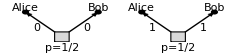

```mathematica
Block[{bg,str},
bg={{Arrowheads[{{0.05,0.85}}],Arrow[{{0,0},{5,5}}],Arrow[{{0,0},{-5,5}}]},{Disk[#,0.5]&/@{{-5,5},{5,5}}},{EdgeForm[Black],LightGray,Rectangle[{-1,-1},{1,1},RoundingRadius->.5]},
{Text["Alice",{-5,5},{0,-1.2}],Text["Bob",{5,5},{0,-1.2}]},
Text["\!\(p=1/2\)",{0,-1},{0,1}]};
str[bs_]:=Inset[Grid[{bs},Alignment->{Center,Center},Frame->All,FrameStyle->Thin,Spacings->{0.05,0}],{#,3},{-Sign[#],1}]&/@{-3,3};
Graphics[{Translate[{bg,str[{"0"}]},{-8,0}],Translate[{bg,str[{"1"}]},{8,0}]},ImageSize->240]]
```

If Alice and Both both measure σ^x, they will find

σ_A^x=σ_B^x=Piecewise[{{+1, p=1/2}, {-1, p=1/2}}].

Quantum explanation: can be inferred from ⟨σ_A^x⟩=⟨σ_B^x⟩=0 and ⟨σ_A^x σ_B^x⟩=1.

To model this classically: we will need to introduce another hidden variable to encode the perfect correlation in σ^x channel.

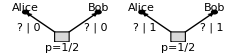

```mathematica
Block[{bg,str},
bg={{Arrowheads[{{0.05,0.85}}],Arrow[{{0,0},{5,5}}],Arrow[{{0,0},{-5,5}}]},{Disk[#,0.5]&/@{{-5,5},{5,5}}},{EdgeForm[Black],LightGray,Rectangle[{-1,-1},{1,1},RoundingRadius->.5]},
{Text["Alice",{-5,5},{0,-1.2}],Text["Bob",{5,5},{0,-1.2}]},
Text["\!\(p=1/2\)",{0,-1},{0,1}]};
str[bs_]:=Inset[Grid[{bs},Alignment->{Center,Center},Frame->All,FrameStyle->Thin,Spacings->{0.05,0}],{#,3},{-Sign[#],1}]&/@{-3,3};
Graphics[{Translate[{bg,str[{"?","0"}]},{-8,0}],Translate[{bg,str[{"?","1"}]},{8,0}]},ImageSize->240]]
```

As Alice and Bob can choose to measure either σ^z or σ^x at their free will ⇒ Classically, both hidden variables about σ^z and σ^x must be sent with the qubit. (Although a single EPR state is sufficient to explain all situations in the quantum way).

If Alice measures σ_A^z and Bob measures σ_B^x, they will find independently that

σ_A^z=Piecewise[{{+1, p=1/2}, {-1, p=1/2}}], σ_B^x=Piecewise[{{+1, p=1/2}, {-1, p=1/2}}].

Quantum explanation: can be inferred from ⟨σ_A^z⟩=⟨σ_B^x⟩=0 and ⟨σ_A^z σ_B^x⟩=0.

The classical hidden variables can reproduce this behavior only if they follow the joint distribution

Alice | Bob | p
00 | 00 | 1/4
01 | 01 | 1/4
10 | 10 | 1/4
11 | 11 | 1/4

So far so good. But Alice and Bob can also decide to measure σ^y, or more generally, any linear combination of their observables … What if Alice measures n_A·σ_A and Bob measures n_B·σ_B? (where n_A and n_B are unit vectors) Their outcomes will follow the joint distribution

n_A·σ_A | n_B·σ_B | p
+1 | +1 | (1+n_A·n_B)/4
+1 | -1 | (1-n_A·n_B)/4
-1 | +1 | (1-n_A·n_B)/4
-1 | -1 | (1+n_A·n_B)/4

The probability that Alice and Bob obtain the same outcome is

p(n_A·σ_A=n_B·σ_B)=(1+n_A·n_B)/2.

Quantum explanation: can be inferred from ⟨n_A·σ_A⟩=⟨n_B·σ_B⟩=0 and ⟨n_A·σ_An_B·σ_B⟩=n_A·n_B.

Classically, to reproduce all these, we will need many (could be infinitely many) hidden variables. (This is ugly but not fatal yet.)

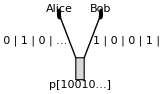

```mathematica
Block[{bg,str},
bg={{Arrowheads[{{0.12,0.85}}],Arrow[{{0,0},{5,5}}],Arrow[{{0,0},{-5,5}}]},{Disk[#,0.5]&/@{{-5,5},{5,5}}},{EdgeForm[Black],LightGray,Rectangle[{-1,-1},{1,1},RoundingRadius->.5]},
{Text["Alice",{-5,5},{0,-1.2}],Text["Bob",{5,5},{0,-1.2}]}};
str[bs_]:=Inset[Grid[{bs},Alignment->{Center,Center},Frame->All,FrameStyle->Thin,Spacings->{0.05,0}],{#,3},{-Sign[#],1}]&/@{-3,3};
Graphics[{bg,str[{"1","0","0","1","0","…"}],Text["\!\(p[10010…]\)",{0,-1},{0,1}]},ImageSize->160]]
```

There should be complicated correlation among hidden variables in an attempt to match quantum predictions (but the attempt may fail). Suppose two of the hidden variables happen to determine the outcome of n_1·σ and n_2·σ. After marginalize (sum) over all the other hidden variables, the marginal distribution should be

Alice | Bob | p
…00… | …00… | (1+n_1·n_2)/4
…01… | …01… | (1-n_1·n_2)/4
…10… | …10… | (1-n_1·n_2)/4
…11… | …11… | (1+n_1·n_2)/4.

Now consider Alice and Bob can choose to measure any one of the three observables n_1·σ, n_2·σ and n_3·σ (on their own qubits respectively, where n_(1,2,3) are unit vectors).

Classically, there must be three hidden variables associated with the three observables, following some marginal distribution

Alice | Bob | p
…000… | …000… | p_1
…001… | …001… | p_2
…010… | …010… | p_3
…011… | …011… | p_4
…100… | …100… | p_5
…101… | …101… | p_6
…110… | …110… | p_7
…111… | …111… | p_8.

The probability must sum up to 1, i.e.

p_1+p_2+…+p_8=1.

If Alice measures n_1·σ_A and Bob measures n_2·σ_B, the probability that they obtain the same outcome is

p(n_1·σ_A=n_2·σ_B)=p_1+p_2+p_7+p_8.

If Alice measures n_2·σ_A and Bob measures n_3·σ_B, the probability that they obtain the same outcome is

p(n_2·σ_A=n_3·σ_B)=p_1+p_4+p_5+p_8.

If Alice measures n_3·σ_A and Bob measures n_1·σ_B, the probability that they obtain the same outcome is

p(n_3·σ_A=n_1·σ_B)=p_1+p_3+p_6+p_8.

Put together,

p(n_1·σ_A=n_2·σ_B)+p(n_2·σ_A=n_3·σ_B)+p(n_3·σ_A=n_1·σ_B)
=3 p_1+p_2+p_3+p_4+p_5+p_6+p_7+3 p_8
=1+2 p_1+2 p_8

This leads to a (version of) Bell inequality.

p(n_1·σ_A=n_2·σ_B)+p(n_2·σ_A=n_3·σ_B)+p(n_3·σ_A=n_1·σ_B)≥1.

A diagrammatic illustration:

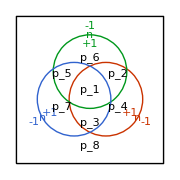

```mathematica
Graphics[{{EdgeForm[Directive[Black,AbsoluteThickness[1]]],White,Rectangle[{-4,-4},{4,4}]},{{#1,Circle[#2,2],Block[{tilt={Abs[#1],#2}&@@({{0,-1},{1,0}}.#2)},{Text[Style["\!\(n\_"<>#3<>"·σ\)",Background->White],3#2,{0,0},tilt],Text["\!\(+1\)",2.5#2,{0,0},tilt],Text["\!\(-1\)",3.5#2,{0,0},tilt]}]}&@@@Thread[{{Red,Green,Blue},CirclePoints[3],ToString/@Range[3]}]},
Text["\!\(p\_"<>#2<>"\)",1.75#1]&@@@Thread[{CirclePoints[3],ToString/@{4,6,7}}],Text["\!\(p\_"<>#2<>"\)",1.75#1]&@@@Thread[{CirclePoints[{1,π/6},3],ToString/@{2,5,3}}],
Text["\!\(p\_1\)",{0,0}],Text["\!\(p\_8\)",{0,-3}]},ImageSize->180]
```

Now what is the quantum mechanical prediction? Recall the quantum result in Eq. (DisplayFormulaNumbered), the Bell inequality would require

(1+n_1·n_2)/2+(1+n_2·n_3)/2+(1+n_3·n_1)/2≥1,

for three unit vectors n_1, n_2 and n_3.

Consider a special case, where the three vectors are 120° to each other in a plane.

```mathematica
Graphics[{Arrowheads[0.2],{Arrow[{{0,0},#1}],Text["\!\(n\_"<>#2<>"\)",#1,-#1]}&@@@Thread[{CirclePoints[3],ToString/@Range[3]}]},ImageSize->80]
```

-Graphics-

n_1·n_2=n_2·n_3=n_3·n_1=-1/2.

Then Eq. (DisplayFormulaNumbered) would require

1/4+1/4+1/4=3/4≥1,

which is not true.

The violation of Bell inequality indicates that no classical model of local hidden variables can ever reproduce all the predictions of quantum mechanics. This is the Bell’s theorem.

How does Bell inequality tell us about entanglement?

Consider a two qubit state ψ=cos α↑↑+sin α↓↓, where α is a phase angle.
(i) Calculate the 2nd Rényi entanglement entropy S^(2)(A) of qubit A (as a function of α).
(ii) Use the observables defined in Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) to evaluate ψ σ_A ψ, ψ σ_B ψ and ψσ_A⊗σ_Bψ.
(iii) Let n_1, n_2, n_3 be three unit vectors 120° to each other in the xz plane, evaluate the left-hand-side of the Bell inequality
 p(n_1·σ_A=n_2·σ_B)+p(n_2·σ_A=n_3·σ_B)+p(n_3·σ_A=n_1·σ_B)
as a function of α.

We can plot the l.h.s. of the Bell inequality v.s. the 2nd Rényi entanglement entropy for different α:

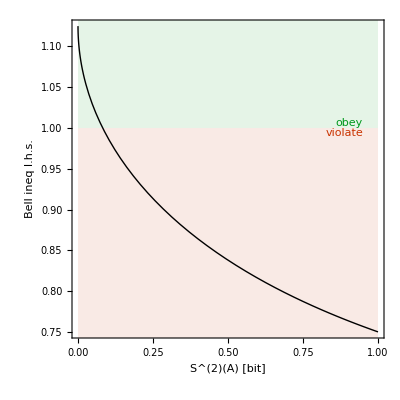

```mathematica
ParametricPlot[{-Log[2,Cos[α]^4+Sin[α]^4],3/8(3-Sin[2α])},{α,0,π/4},AspectRatio->1,PlotStyle->Black,PlotRangePadding->0.01,Prolog->{Opacity[0.1],{Red,Polygon[{{0,1},{1,1},{1,0},{0,0}}]},{Green,Polygon[{{0,1},{1,1},{1,2},{0,2}}]}},GridLines->{{-Log[2,Cos[#]^4+Sin[#]^4]&[ArcSin[1/3]/2]},{1}},
FrameLabel->{"\!\(S\^(2)(A)\) [bit]","Bell ineq l.h.s."},
Epilog->{{Red,Text["violate",{0.95,1},{1,1}]},{Green,Text["obey",{0.95,1},{1,-1}]}}]
```

For pure state, such as ψ in the above example, entanglement entropy S^(2)(A)>0 ⇔ the state is entangled. But the Bell inequality is not always violated. ⇒ It is an entanglement witness.

For mixed state, entropy no longer provides a good measure of quantum entanglement. We had to rely on Bell inequalities and other entanglement witness.

### Quantum Many-Body Systems

#### Combining Systems

Tensor product of states. Suppose ψ=∑_i ψ_i i_A, ϕ=∑_j ϕ_j j_B

ψ⊗ϕ=∑_(i,j) ψ_i ϕ_j i_A⊗j_B=∑_(i,j) ψ_i ϕ_j ij.

Note: the double index ij labels a single state ij.

Rule of inner product.

ijkl=j_B⊗i_Ak_A⊗l_B=ik_A jl_B=δ_ik δ_jl.

Tensor product of operators. Suppose A=∑_(i,j) i_A A_ij j_A, B=∑_(k,l) k_B B_kl l_B,

A⊗B=∑_(i,j,k,l) A_ij B_kl i_A k_B⊗l_B j_A
=∑_(i,j,k,l) A_ij B_kl ik⊗lj.

Axiom 5 (Composition): The Hilbert space of a combined quantum system is the direct product of the Hilbert space of each subsystem.

Suppose systems A and B are associated with the Hilbert spaces ℋ_A and ℋ_B respectively,

ℋ_A=span{i_A}, ℋ_B=span{j_B},

the composite system A∪B will be associated with the Hilbert space

ℋ_(A∪B)=ℋ_A⊗ℋ_B=span{i_A⊗j_B}=span{ij}.

Hilbert space tensor product ⇒ Hilbert space dimension multiplies

dim ℋ_(A∪B)=dim ℋ_A dim ℋ_B.

Generic states in ℋ_(A∪B)

ψ=∑_(i,j) ψ_ij ij.

Generic operators in ℋ_(A∪B)

L=∑_(i,j,k,l) ij L_(ij,kl)kl,

where the matrix (tensor) element

L_(ij,kl)=ijLkl.

#### Tensor Network and Quantum Circuit

Complicated quantum systems can be built out of qubits.

Many-body Hilbert space ℋ=ℋ_1⊗ℋ_2⊗ℋ_3⊗…

States in ℋ

ψ=∑_(i_1 i_2…) ψ_(i_1 i_2…)i_1 i_2…=∑_[i] ψ_[i][i].

Notation: bundled index [i]=i_1 i_2….

Operators in ℋ

L=∑_(i_1 i_2…) ∑_(j_1 j_2…) i_1 i_2…L_(i_1 i_2…,j_1 j_2…)j_1 j_2…
=∑_([i],[j]) [i]L_([i][j])[j].

States and operators are both represented as tensors in general. Note: the tensor here is just a multi-dimensional array, without the requirement of covariance as in general relativity.

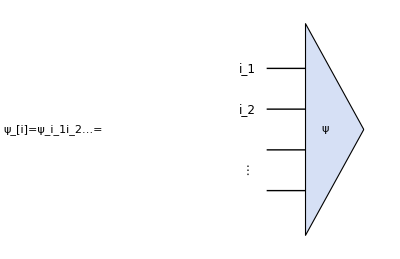

```mathematica
Block[{n=3,ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Text["\!\(ψ\_[i]=ψ\_\(i\_1i\_2…\)=\)",{-7,0}],Table[Line[{#,y}&/@{-1.5,0}],{y,-1.5,1.5}],ket["ψ"],Text[Style[#1,12],{-2,#2}]&@@@{{"\!\(i\_1\)",1.5},{"\!\(i\_2\)",0.5},{"⋮",-1
}}},ImageSize->{Automatic,60}]]
```

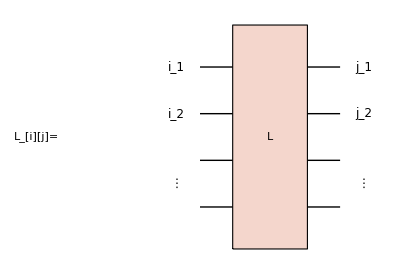

```mathematica
Block[{n=3,ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Text["\!\(L\_\([i][j]\)=\)",{-5,0}],Table[Line[{#,y}&/@{-1.5,1.5}],{y,-1.5,1.5}],opH["L"],Text[Style[#1,12],{-2,#2}]&@@@{{"\!\(i\_1\)",1.5},{"\!\(i\_2\)",0.5},{"⋮",-1
}},Text[Style[#1,12],{2,#2}]&@@@{{"\!\(j\_1\)",1.5},{"\!\(j\_2\)",0.5},{"⋮",-1
}}},ImageSize->{Automatic,60}]]
```

Tensor product: simply put the tensors together.

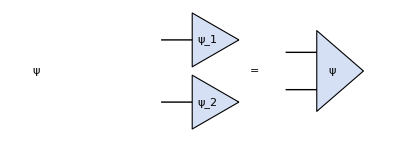

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0},n_:1]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0},n_:1]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0},n_:1]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0},n_:1]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Text["\!\(ψ=ψ_1⊗ψ_2=\)",{-5.5,0}],
Translate[{Line[{#,0}&/@{-1.5,0}],ket["ψ\_"<>#2]},{0,#}]&@@@{{-1,"2"},{1,"1"}},Text["=",{1.5,0}],
Translate[{Line[{{#,0.6}&/@{-1.5,0},{#,-0.6}&/@{-1.5,0}}],ket["ψ",{0,0},1.5]},{4,0}]},ImageSize->{Automatic,60}]]
```

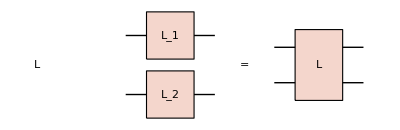

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0},n_:1]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0},n_:1]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0},n_:1]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0},n_:1]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Text["\!\(L=L_1⊗L_2=\)",{-4.5,0}],
Translate[{Line[{#,0}&/@{-1.5,1.5}],opH["L\_"<>#2]},{0,#}]&@@@{{-1,"2"},{1,"1"}},Text["=",{2.5,0}],
Translate[{Line[{{#,0.6}&/@{-1.5,1.5},{#,-0.6}&/@{-1.5,1.5}}],opH["L",{0,0},1.5]},{5,0}]},ImageSize->{Automatic,60}]]
```

Tensor Contraction: indices on internal legs are automatically summed over.

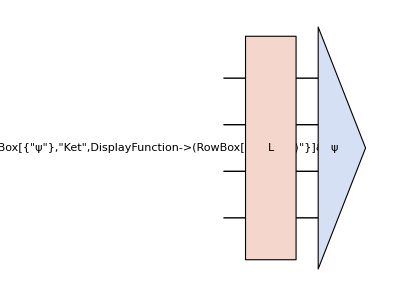

```mathematica
Block[{n=3,ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Text["\!\(Lψ=\)",{-4,0}],Table[Line[{#,y}&/@{-1.5,2}],{y,-1.5,1.5}],opH["L"],ket["ψ",{2,0}]},ImageSize->{Automatic,60}]]
```

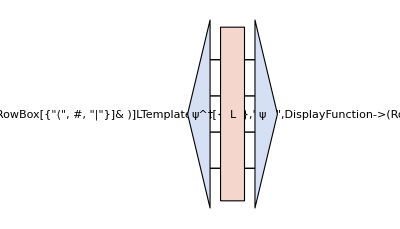

```mathematica
Block[{n=3,ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Text["\!\(ψLψ=\)",{-6,0}],Table[Line[{#,y}&/@{-2,2}],{y,-1.5,1.5}],bra["ψ\^†",{-2,0}],opH["L"],ket["ψ",{2,0}]},ImageSize->{Automatic,60}]]
```

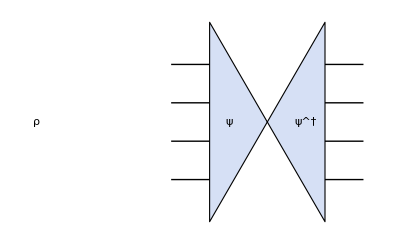

```mathematica
Block[{n=3,ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Text["\!\(ρ=ψψ=\)",{-6,0}],Table[Line[{{#,y}&/@{-2.5,-1},{#,y}&/@{1,2.5}}],{y,-1.5,1.5}],ket["ψ",{-1,0}],bra["ψ\^†",{1,0}]},ImageSize->{Automatic,60}]]
```

(Partial) Trace: connect the pair of legs to be traced.

ρ_A=Tr_(Ā)ψψ.

```mathematica
Block[{n=1.2,ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Translate[{Line[{{#,0.5}&/@{-2.5,-1},{#,0.5}&/@{1,2.5}}],BSplineCurve[{{-1,-0.5},{-2,-0.5},{-2.5,-0.5},{-2.5,-1},{-2.5,-1.5},{-2,-1.5},{-1,-1.5},{1,-1.5},{2,-1.5},{2.5,-1.5},{2.5,-1},{2.5,-0.5},{2,-0.5},{1,-0.5}}],ket["ψ",{-1,0}],bra["ψ\^†",{1,0}]},{-4,0}],
Text["="],
Translate[{Line[{{#,-0.5}&/@{-2,2}}],Scale[BSplineCurve[{{-2,0.5},{-1,0.5},{-0.5,0.5},{0,1},{0.5,1.5},{1,1.5},{2.5,1.5}}],{#,1},{0,1}]&/@{-1,1},bra["ψ\^†",{-2,0}],ket["ψ",{2,0}]},{4,0}]},ImageSize->{Automatic,50}]]
```

-Graphics-

Let us try to express the 2nd Rényi entropy

e^(-S^(2)(A))=Tr_A ρ_A^2
=(Tr(ψψ))^(⊗2)(X_A⊗𝟙_(Ā))
=ψ^(⊗2)(X_A⊗𝟙_(Ā))ψ^(⊗2).

The ⊗ and ⊗ tensor products have different meanings. This ambiguity can be resolved by the tensor network.

```mathematica
Block[{n=1.2,ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Translate[{Text["Tr",{-6,0}],Scale[BSplineCurve[{{-2,2},{-1,2},{-0.5,2},{0.5,-1},{1,-1},{2,-1}}],{#,1},{0,0}]&/@{-1,1},Line[{{-2,#},{2,#}}]&/@{1,-2},Line[{{-5,#},{-4,#}}]&/@{-2,-1,1,2},bra["ψ\^†",{-2,1.5}],ket["ψ",{-4,1.5}],bra["ψ\^†",{-2,-1.5}],ket["ψ",{-4,-1.5}]},{-3,0}],Text["="],Translate[{Scale[BSplineCurve[{{-2,2},{-1,2},{-0.5,2},{0.5,-1},{1,-1},{2,-1}}],{#,1},{0,0}]&/@{-1,1},Line[{{-2,#},{2,#}}]&/@{1,-2},bra["ψ\^†",{-2,1.5}],ket["ψ",{2,1.5}],bra["ψ\^†",{-2,-1.5}],ket["ψ",{2,-1.5}]},{4,0}]},ImageSize->{Automatic,75}]]
```

-Graphics-

Diagonalization or Singular Value Decomposition (SVD).

For Hermitian operator, decompose by matrix diagonalization,

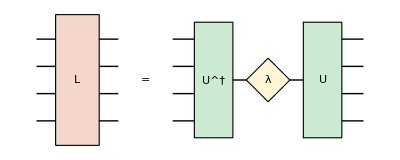

```mathematica
Block[{n=3,ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Table[Line[{#,y}&/@{-1.5,1.5}],{y,-1.5,1.5}],opH["L"],Text["=",{2.5,0}],Translate[{Table[Line[{{#,y}&/@{-3.5,-2},{#,y}&/@{3.5,2}}],{y,-1.5,1.5}],Line[{{-2,0},{2,0}}],opU["U\^†",{-2,0}],opD["λ",{0,0}],opU["U",{2,0}]},{7,0}]},ImageSize->{Automatic,60}]]
```

For more general tensors, decompose by SVD.

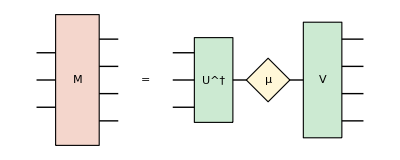

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Table[Line[{#,y}&/@{-1.5,0}],{y,-1,1}],Table[Line[{#,y}&/@{0,1.5}],{y,-1.5,1.5}],opH["M",3],Text["=",{2.5,0}],Translate[{Table[Line[{#,y}&/@{-3.5,-2}],{y,-1,1}],Table[Line[{#,y}&/@{3.5,2}],{y,-1.5,1.5}],Line[{{-2,0},{2,0}}],opU["U\^†",2.2,{-2,0}],opD["μ",{0,0}],opU["V",3,{2,0}]},{7,0}]},ImageSize->{Automatic,60}]]
```

Mix state purification: given a mixed state density matrix ρ, find a pure state ψ (in a larger Hilbert space), such that its reduced density matrix reproduces ρ. The procedure is to first diagonalize ρ and split its eigenvalues in square roots p_i=p_i^(1/2)p_i^(1/2).

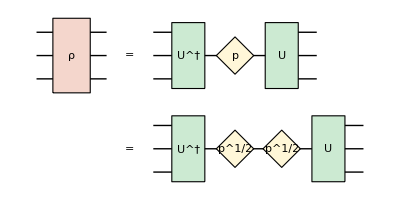

```mathematica
Block[{n=2,ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0},shift_:{0,0.2}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},shift]},pos];
Graphics[{Table[Line[{#,y}&/@{-1.5,1.5}],{y,-1,1}],opH["ρ"],Text["=",{2.5,0}],Translate[{Table[Line[{{#,y}&/@{-3.5,-2},{#,y}&/@{3.5,2}}],{y,-1,1}],Line[{{-2,0},{2,0}}],opU["U\^†",{-2,0}],opD["p",{0,0}],opU["U",{2,0}]},{7,0}],
Text["=",{2.5,-4}],
Translate[{Table[Line[{{#,y}&/@{-4.5,-3},{#,y}&/@{4.5,3}}],{y,-1,1}],Line[{{-3,0},{3,0}}],opU["U\^†",{-3,0}],opD["p\^\(1\/2\)",{-1,0},{-0.3,-0.2}],opD["p\^\(1\/2\)",{1,0},{-0.3,-0.2}],opU["U",{3,0}]},{8,-4}]},ImageSize->{Automatic,90}]]
```

Take one square root and bend around the unitary ⇒ the purified state ψ. It is also called the thermal field double state, if p follows the thermal equilibrium distribution, i.e. p_i∝e^(-β E_i).

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0},shift_:{0,0.2}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},shift]},pos];
Graphics[{
Translate[{Table[Line[{{#,y}&/@{-1.5,0}}],{y,DeleteCases[Range[-3,3],0]}],BSplineCurve[{{0,2},{1,2},{2,2},{2,1},{2,0},{2,-1},{2,-2},{1,-2},{0,-2}}],opU["U\^†",2,{0,2}],opD["p\^\(1\/2\)",{2,0},{-0.3,-0.2}],opU["Uᵀ",2,{0,-2}]},{-4,0}],
Text["="],Translate[{Table[Line[{{#,y}&/@{-1.5,-0.5}}],{y,DeleteCases[Range[-3,3],0]}],ket["ψ",4,{0,0}]},{2,0}]},ImageSize->{Automatic,90}]]
```

-Graphics-

Tensor network: a collection of tensors connected by contractions.

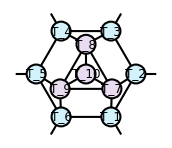

```mathematica
Block[{vsf},
vsf[col_]:=Function[{p,v,b},{{EdgeForm[Directive[Black,Opacity[1],AbsoluteThickness[1.5]]],Lighter[col,0.8],Disk[p,b]},{Black,Text[Style["\!\(T\_"<>ToString[v]<>"\)",12],p]}}];
Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,7<->1,7<->2,8<->3,8<->4,9<->5,9<->6,7<->8,8<->9,9<->7,10<->7,10<->8,10<->9,11<->1,12<->2,13<->3,14<->4,15<->5,16<->6},VertexCoordinates->Join[CirclePoints[6],0.6CirclePoints[3],{{0,0}},1.6CirclePoints[6]],
VertexShapeFunction->Flatten[{#->vsf[Cyan]&/@{1,2,3,4,5,6},#->vsf[Purple]&/@{7,8,9,10},(#->({}&)&)/@{11,12,13,14,15,16}}],VertexSize->{"Scaled",0.09},EdgeStyle->Directive[Black,Opacity[1],AbsoluteThickness[1.5]],ImageSize->172]]
```

Efficient representation of big tensors ⇒ numerical method to solve quantum many-body problems.

Conceptual tools to visualize the entanglement structures and symmetry properties ⇒ tensor network holography, tensor network formulation of topological order.

Quantum circuits are a subclass of tensor networks.

Each wire: a qubit.

Each block: a unitary operator, also called a quantum gate.

Example: a simple quantum circuit that prepares Bell states.

```mathematica
Graphics[{Line[{{-2,#},{2,#}}&/@{-1,1}],Translate[Block[{a=0.5},{{EdgeForm[Directive[Black,AbsoluteThickness[1]]],White,Rectangle[{-a,-a},{a,a}]},Text[Style["H",FontFamily->"CMU Sans Serif"]]}],{-0.8,1}],Translate[Block[{r=0.5},{{EdgeForm[Directive[Black,AbsoluteThickness[0.8],Dashed]],Opacity[0],Rectangle[{-1.5r,-1-1.5r},{1.5r,1+1.5r},RoundingRadius->r]},PointSize[0.1],Point[{0,1}],Line[{{0,1},{0,-1-r}}],Circle[{0,-1},r]}],{0.8,0}]},ImageSize->80]
```

-Graphics-

It consists of two tensors: a Hadamard gate (H) and a controlled NOT gate (CNOT, in the dashed region)

H≏1/(√2)(1 | 1
1 | -1),
CNOT≏(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0).

Convention: for quantum circuit, the state enters from left, and exits form right.

What are the resulting states when the above quantum circuit acts on (i) the state ↑↑ and (ii) the state ↓↓?

#### Quantum Decoherence

Consider a qubit coupled to a bath.

System A: a qubit → two-dimensional Hilbert space

ℋ_A=span{↑,↓},

System B: a bath → d-dimensional Hilbert space (d is supposed to be large)

ℋ_B=span{i}_(i=1,…,d)

The Hilbert space of the combined system

ℋ=ℋ_A⊗ℋ_B=span{↑⊗i,↓⊗i}_(i=1,…,d).

Suppose the interaction between the qubit and the bath is described by the Hamiltonian

H=σ^z⊗M,

where M is a Hermitian operator acting on ℋ_B (or represented as a d×d Hermitian matrix).

Initial state: a product state of qubit ρ_A and bath ρ_B

ρ(0)=ρ_A(0)⊗ρ_B(0).

Evolve the system with H by time t,

ρ(t)=U(t)ρ(0)(U(t))^†,

where U(t)=e^(-ⅈ H t)=e^(-ⅈ σ^z⊗M t).

Goal: trace out the bath and focus on the reduced density matrix of the qubit

ρ_A(t)=Tr_B ρ(t).

In general, recall Eq. (DisplayFormulaNumbered), ρ_A(t) takes the form

ρ_A(t)=1/2(𝟙+⟨σ(t)⟩·σ).

Alternatively, we just need to determine ⟨σ(t)⟩, which is directly related to physical observables.

##### Numerics

Start by setting up a d×d random Hermitian matrix M

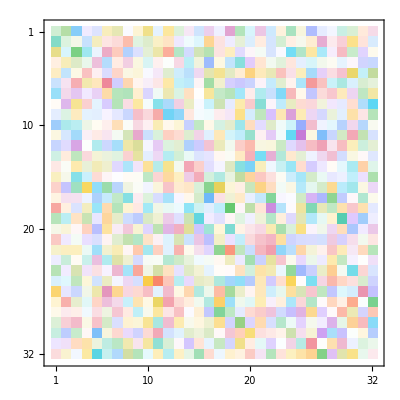

```mathematica
d=32;
M=(#+ConjugateTranspose[#])/2&[RandomVariate[NormalDistribution[0,1/Sqrt[d]],{d,d,2}].{1,ⅈ}];
ComplexMatrixPlot@M
```

Construct the Hamiltonian and then define the unitary operator

```mathematica
H=KroneckerProduct[PauliMatrix[3],M];
U[t_]:=MatrixExp[-ⅈ H t];
```

Prepare a initial state

ρ(0)=ψ(0)ψ(0),
ψ(0)=(3↑+4↓)/5⊗1.

```mathematica
ψ0=Flatten[({3,4}/5)⊗SparseArray[{1->1},d]];
```

Evolve the state and measure spin expectation values of the qubit

```mathematica
ψ[t_]:=U[t].ψ0;
spin[t_]:=Re@Table[Conjugate[#].KroneckerProduct[PauliMatrix[a],IdentityMatrix[d]].#,{a,3}]&@ψ[t];
spin[0]
spin[10]
```

{0.96,0.,-0.28}

{-0.00414468,-0.0768878,-0.28}

Plot the spin expectation values (in log time scale)

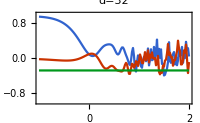

```mathematica
ListLinePlot[Thread@Table[{lgt,#}&/@spin[10^lgt],{lgt,-1,2,0.02}],PlotLabel->"\!\(d="<>ToString[d]<>"\)",FrameLabel->{"\!\(lg t\)","\!\(⟨σ(t)⟩\)"},PlotRange->{-1,1},PlotLegends->(Style["\!\(⟨σ\^"<>#<>"⟩\)",FontFamily->"CMU"]&/@{"x","y","z"}),ImageSize->200]
```

With a larger bath (5 qubits → 9 qubits), the fluctuation is quickly suppressed.

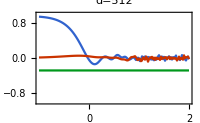

```mathematica
Block[{d=512,M,H,Es,ψs,ψ0,lgts,projs,ψts,ρs},
M=(#+ConjugateTranspose[#])/2&[RandomVariate[NormalDistribution[0,1/Sqrt[d]],{d,d,2}].{1,ⅈ}];
H=KroneckerProduct[SparseArray@PauliMatrix[3],M];
{Es,ψs}=Eigensystem@H;
ψ0=Flatten[Normalize[{3,4}]⊗SparseArray[{1->1},d]];
lgts=Range[-1,2,0.02];
projs=Conjugate[ψs].ψ0;
ψts=Table[projs Exp[-ⅈ Es 10^lgt],{lgt,lgts}].ψs;
ρs=#.ConjugateTranspose[#]&/@ArrayReshape[ψts,{Length@lgts,2,d}];
ListLinePlot[Thread[{lgts,#}]&/@Thread[Table[Re@Tr[PauliMatrix[a].#],{a,3}]&/@ρs],PlotLabel->"\!\(d="<>ToString[d]<>"\)",FrameLabel->{"\!\(lg t\)","\!\(⟨σ(t)⟩\)"},PlotRange->{-1,1},PlotLegends->(Style["\!\(⟨σ\^"<>#<>"⟩\)",FontFamily->"CMU"]&/@{"x","y","z"}),ImageSize->200]]
```

Observations:

As time evolves, ⟨σ^x⟩, ⟨σ^y⟩ decays to zero (+ fluctuations) in 𝒪(1) time.

⟨σ^z⟩ is conserved (since [σ^z,H]=0).

The consequence is that the off-diagonal elements of ρ_A decays with time ⇒ decoherence of the qubit under the interaction with a bath. Note: the diagonal basis is set by how the qubit is coupled to the bath (if H=σ^x⊗M then ⟨σ^y⟩ and ⟨σ^z⟩ will decay, and the eigenbasis of σ^x is the diagonal basis).

In general, if a qubit couples to a bath via a spin operator n·σ as

H=n·σ⊗M,

under unitary time evolution e^(-ⅈ H t) of the combined system, its spin expectation value ⟨σ⟩ will decay to (⟨σ⟩·n)n, i.e.

⟨σ(t)⟩⟶^(t≫1)(⟨σ(0)⟩·n)n,

which effectively projects the initial spin expectation value ⟨σ(0)⟩ to the direction n.

More generally, if there are more than one coupling channels in the Hamiltonian

H=n_1·σ⊗M_1+n_2·σ⊗M_2,

where M_1 and M_2 are independently random, then the spin expectation value ⟨σ⟩ will decay to zero as long as |n_1·n_2|<1. An intuitive understanding: ⟨σ⟩ is projected towards n_1 or n_2 repeatedly, ⇒ Its magnitude |⟨σ⟩| always decays. ⇒ Eventually, it will decay to zero, i.e.

⟨σ(t)⟩⟶^(t≫1)0.

In this case, the qubit decohere to the maximally mixed state.

The decoherence of the qubit is also reflected in the growth of its entanglement entropy.

S_A(t)=-Tr ρ_A(t)ln ρ_A(t).

ρ_A evolves from a pure state (S_A=0) to a mixed state (S_A>0).

The qubit-bath coupling entangles the qubit with the bath under unitary time evolution. ⇒ Quantum information of the qubit (partially) spread into the bath via the quantum entanglement. For the qubit itself, as if the information is lost ⇒ entropy must grow.

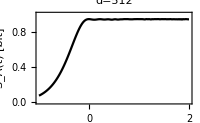

```mathematica
Block[{d=512,M,H,Es,ψs,ψ0,lgts,projs,ψts,ρs},
M=(#+ConjugateTranspose[#])/2&[RandomVariate[NormalDistribution[0,1/Sqrt[d]],{d,d,2}].{1,ⅈ}];
H=KroneckerProduct[SparseArray@PauliMatrix[3],M];
{Es,ψs}=Eigensystem@H;
ψ0=Flatten[Normalize[{3,4}]⊗SparseArray[{1->1},d]];
lgts=Range[-1,2,0.02];
projs=Conjugate[ψs].ψ0;
ψts=Table[projs Exp[-ⅈ Es 10^lgt],{lgt,lgts}].ψs;
ρs=#.ConjugateTranspose[#]&/@ArrayReshape[ψts,{Length@lgts,2,d}];
ListLinePlot[Thread@{lgts,-Tr[#.MatrixLog[#]]/Log[2]&/@ρs},PlotStyle->Black,PlotLabel->"\!\(d="<>ToString[d]<>"\)",FrameLabel->{"\!\(lg t\)","\!\(S\_A(t)\) [bit]"},PlotRange->{0,1},ImageSize->200]]
```

##### Theory*

We do not want to specify what M really is ⇒ M is a random Hermitian matrix, draw from the Gaussian unitary ensemble, meaning that the probability density of M is given by

p(M)∝exp(-d/2Tr M^2),

subject to the Hermitian condition M=M^†. Several properties from random matrix theory:

If we diagonalize M

M=V E V^†,

such that E=diag(E_n) is the diagonal matrix. V will be a Haar random unitary matrix and E_n follows the semi-circle law:

p(E_n)=1/(2π)√(4-E_n^2).

Fourier transform of the semi-circle distribution defines the spectral form factor

Φ(t)=∫ⅆE p(E)e^(-ⅈ E t)=(J_1(2t))/t,

where J_1 is the Bessel function.

With the spectral decomposition Eq. (DisplayFormulaNumbered),

U(t)=V e^(-ⅈ σ_z E t)V^† | (U(t))^†=V e^(ⅈ σ_z E t)V^†
=, | =.

Represent the density matrices ρ_A and ρ_B as small and large circles

ρ_A=, ρ_B=,

tensor product simply combines them together

ρ=ρ_A⊗ρ_B=.

Under time evolution, the reduced density matrix ρ_A(t) reads

ρ_A(t)=Tr_B U(t)ρ (U(t))^†
==

The formula to average (a pair of) d×d Haar random unitary matrices

avg=1/d.

Argument for Eq. (DisplayFormulaNumbered):

SU(d) symmetry: ∀U∈SU(d),

avg=avg=avg.

This pins down the form of the average up to an overall factor c,

avg=c

The factor c can be determined by considering

avg=avg=avg d=d,
avg=c=c d^2,

to be consistent, must have d=c d^2, so c=d^-1.

Using Eq. (DisplayFormulaNumbered), the ensemble average reduces Eq. (DisplayFormulaNumbered) to

avg ρ_A(t)=1/d.

The two phase matrices  and  are controlled by the qubit operators.

If both σ^z are of the same sign, then

avg e^(-ⅈ σ_z E t)e^(ⅈ σ_z E t)=avg 1=1.

If the two σ^z are of opposite sign

avg e^(-ⅈ σ_z E t)e^(ⅈ σ_z E t)=avg e^(±2ⅈ E t)=avg F(t).

Therefore

avg ρ_A(t)=1/2(ρ_A+σ^z ρ_A σ^z)+1/2 avg F(t)(ρ_A-σ^z ρ_A σ^z).

The function F(t) has the following statistics

avg F(t)=Φ(2t),
var F(t)=(d γ-1)/(d^2-1)(1-2(Φ(2t))^2+Φ(4t))/2,

where Φ(t) is the spectral form factor given in Eq. (DisplayFormulaNumbered) and γ=Tr ρ_B^2 is the purity of the bath. Take d=32 (yellow) and d=512 (red), the theory (avg±2std) nicely explains the numerical behavior.

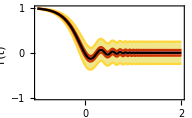

```mathematica
Block[{γ=1,Φ,avg,var,std,ub,lb},
Φ[t_]:=BesselJ[1,2 t]/t;
avg[t_]:=Φ[2t];
var[t_,d_]:=(d γ-1)/(d^2-1)(1-2Φ[2t]^2+Φ[4t])/2;
std[t_,d_]:=Sqrt[var[t,d]];
ub[t_,d_]:=avg[t]+2std[t,d];
lb[t_,d_]:=avg[t]-2std[t,d];
Plot[{ub[10^lgt,32],lb[10^lgt,32],ub[10^lgt,512],lb[10^lgt,512],avg[10^lgt]},{lgt,-1,2},PlotStyle->{Yellow,Yellow,Red,Red,Black},Filling->{1->{{2},LightYellow},3->{{4},LightRed}},PlotRange->{-1,1},FrameLabel->{"\!\(lg t\)","\!\(F(t)\)"}]]
```

This curve describes how quantum decoherence happens in time, and how entropy is generated for a qubit by entangling it to the bath. The subject of quantum information dynamics is a frontier of research.

#### Quantum Error Correction

Quantum decoherence posts a serious threat to quantum information processing.

Qubits couple to the environment and decohere inevitably.

In the extreme case, a qubit can become maximally mixed ⇒ An erasure error: the quantum information of the qubit is fully scrambled with the environment, as if the information has been erased.

Quantum error correction: protecting the quantum information from errors by spreading the information into a highly entangled quantum many-body state (which we have access to).

one logical qubit⇌_(decoded to)^(encoded in)many physical qubits.

Logical qubit: the information theoretic qubit (software level), whose basis states are denoted as UnderBar[↑],UnderBar[↓] (with a underline).

Physical qubit: the actual qubit implemented on quantum devices (hardware level).

Even if some physical qubits are corrupted or erased, one can still retrieve the logical qubit from the rest of the physical qubits.

Five-qubit code: a quantum error correction code that encodes one logical qubit into five physical qubits, where the logical qubit is protected against the erasure of any two physical qubits.

The logical qubit states UnderBar[↑],UnderBar[↓] span a code subspace in the physical qubit Hilbert space.

The code subspace is specified by four commuting Pauli operators on the physical qubits:

M_1≏σ^13310,
M_2≏σ^01331,
M_3≏σ^10133,
M_4≏σ^31013.

These operators are called stabilizers, as they stabilize the logical qubit as their common eigenstates of eigenvalue +1, i.e.

∀i:M_i UnderBar[↑]=UnderBar[↑], M_i UnderBar[↓]=UnderBar[↓].

Recall that we can simultaneously diagonalize commuting operators by constructing a many-body Hamiltonian, e.g.

H=-M_1-M_2-M_3-M_4
≏-σ^13310-σ^01331-σ^10133-σ^31013.

The code subspace = the common eigenspace of stabilizers that ∀i:M_i=+1 = the ground state subspace of the Hamiltonian H.

The code subspace is two-dimensional ⇒ can encode a logical qubit. How do we know? 5 qubits, 4 stabilizers: each stabilizer halves the Hilbert space ⇒ the remaining space dimension:

2^5/2^4=2.

Within the code subspace, a choice of the basis is (can be obtained by diagonalize H)

UnderBar[↑]=1/4 (-↓↓↓↓↑-↓↓↓↑↓-↓↓↑↓↓-↓↓↑↑↑-↓↑↓↓↓+↓↑↓↑↑+↓↑↑↓↑-↓↑↑↑↓-↑↓↓↓↓-↑↓↓↑↑+↑↓↑↓↑+↑↓↑↑↓-↑↑↓↓↑+↑↑↓↑↓-↑↑↑↓↓+↑↑↑↑↑),
UnderBar[↓]=1/4 (↓↓↓↓↓-↓↓↓↑↑+↓↓↑↓↑-↓↓↑↑↓+↓↑↓↓↑+↓↑↓↑↓-↓↑↑↓↓-↓↑↑↑↑-↑↓↓↓↑+↑↓↓↑↓+↑↓↑↓↓-↑↓↑↑↑-↑↑↓↓↓-↑↑↓↑↑-↑↑↑↓↑-↑↑↑↑↓)

```mathematica
Block[{U,basis},
U=SparseArray[ⅈ Dot@@
(Represent/@{C4[-σ[2,3,3,1,0]],C4[-σ[0,2,3,3,1]],C4[σ[3,3,1,2,3]],C4[σ[3,3,3,1,2]],C4[σ[3,3,3,3,1]],C4[σ[3,0,3,0,2]],C4[-σ[0,0,0,0,1]],C4[-σ[0,0,0,0,3]]})];
basis=Ket/@StringJoin/@Tuples[{"↑","↓"},5];
Factor[basis.U.Flatten[{1,0}⊗{1,0}⊗{1,0}⊗{1,0}⊗#]]&/@{{1,0},{0,1}}]
```

{1/4 (-↓↓↓↓↑-↓↓↓↑↓-↓↓↑↓↓-↓↓↑↑↑-↓↑↓↓↓+↓↑↓↑↑+↓↑↑↓↑-↓↑↑↑↓-↑↓↓↓↓-↑↓↓↑↑+↑↓↑↓↑+↑↓↑↑↓-↑↑↓↓↑+↑↑↓↑↓-↑↑↑↓↓+↑↑↑↑↑),1/4 (↓↓↓↓↓-↓↓↓↑↑+↓↓↑↓↑-↓↓↑↑↓+↓↑↓↓↑+↓↑↓↑↓-↓↑↑↓↓-↓↑↑↑↑-↑↓↓↓↑+↑↓↓↑↓+↑↓↑↓↓-↑↓↑↑↑-↑↑↓↓↓-↑↑↓↑↑-↑↑↑↓↑-↑↑↑↑↓)}

Logical qubit.

Logical gates: quantum gates that effectively operate on the logical qubit

Z̲ UnderBar[↑]=UnderBar[↑],Z̲ UnderBar[↓]=-UnderBar[↓],
X̲ UnderBar[↑]=UnderBar[↓],X̲ UnderBar[↓]=UnderBar[↑].

Z̲ and X̲ must commute with all stabilizers (to remain in the code subspace), yet not any product of stabilizers (to be nontrivial). One canonical choice is

Z̲≏σ^33333,X̲≏σ^11111,Y̲=ⅈ X̲ Z̲=σ^22222.

It is hard to decohere the logical qubit, because X̲, Y̲, Z̲  are  non-local. ⇒ Their couplings to the environment are typically weak.

A diagrammatic understanding: the unitary matrix U that diagonalize the Hamiltonian H can be viewed as a quantum circuit,

U^†H U=E.

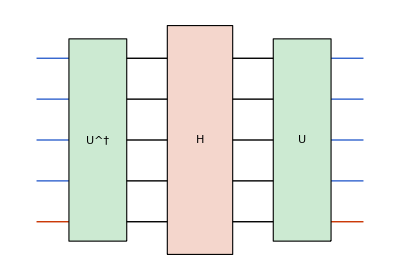

```mathematica
Block[{n=3.5,ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Table[Line[{#,y}&/@{-2,2}],{y,-2,2}],Table[{If[y==-2,Red,Blue],Line[{{#,y}&/@{3,4},{#,y}&/@{-3,-4}}]},{y,-2,2}],opH["H"],opU["U\^†",{-2.5,0}],opU["U",{2.5,0}]},ImageSize->{Automatic,75}]]
```

The quantum circuit U should also simultaneously diagonalize all the stabilizers. With a proper basis choice, one can find U

U≏ⅈ e^(-(ⅈ π)/4 σ^23310)e^(-(ⅈ π)/4 σ^02331)e^((ⅈ π)/4 σ^33123)e^((ⅈ π)/4 σ^33312)e^((ⅈ π)/4 σ^33331)e^((ⅈ π)/4 σ^30302)e^(-(ⅈ π)/4 σ^00001)e^(-(ⅈ π)/4 σ^00003),

such that

U^†M_1 U≏σ^30000,
U^†M_2 U≏σ^03000,
U^†M_3 U≏σ^00300,
U^†M_4 U≏σ^00030.

```mathematica
Block[{U,encode,decode},
U=SparseArray[ⅈ Dot@@
(Represent/@{C4[-σ[2,3,3,1,0]],C4[-σ[0,2,3,3,1]],C4[σ[3,3,1,2,3]],C4[σ[3,3,3,1,2]],C4[σ[3,3,3,3,1]],C4[σ[3,0,3,0,2]],C4[-σ[0,0,0,0,1]],C4[-σ[0,0,0,0,3]]})];
encode[A_]:=Abstract[U.Represent[A].ConjugateTranspose[U]];
decode[A_]:=Abstract[ConjugateTranspose[U].Represent[A].U];
AssociationMap[decode,{σ[1,3,3,1,0],σ[0,1,3,3,1],σ[1,0,1,3,3],σ[3,1,0,1,3],σ[1,1,1,1,1],σ[3,3,3,3,3]}]]
```

<|σ[1,3,3,1,0]→σ[3,0,0,0,0],σ[0,1,3,3,1]→σ[0,3,0,0,0],σ[1,0,1,3,3]→σ[0,0,3,0,0],σ[3,1,0,1,3]→σ[0,0,0,3,0],σ[1,1,1,1,1]→σ[0,0,0,0,1],σ[3,3,3,3,3]→σ[0,0,0,0,3]|>

Decoding stabilizers.

As a result, the Hamiltonian transforms to

U^†H U≏-σ^30000-σ^03000-σ^00300-σ^00030.

The first four qubits are pinned by the Hamiltonian to ↑↑↑↑ to lower the energy ⇒ syndrome qubits.

The last qubit is free ⇒ logical qubit.

The quantum circuit encodes the logical qubit into five physical qubits, given the syndrome qubits pinned to ↑↑↑↑. This is how Eq. (DisplayFormulaNumbered) was obtained.

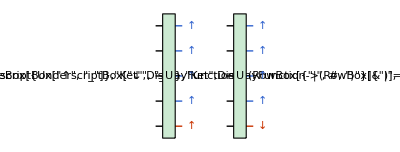

```mathematica
Block[{n=3.5,ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Translate[{Text["\!\(UnderBar[↑]=\)"],Translate[{Table[Line[{#,y}&/@{-1.5,0}],{y,-2,2}],Table[{If[y==-2,Red,Blue],Line[{{#,y}&/@{0,1.5}}]},{y,-2,2}],opU["U",{0,0}],Text[If[#>-2,Style["↑",Blue],Style["↑",Red]],{2,#},{-0.5,0.2}]&/@Range[-2,2]},{3,0}]},{-4,0}],
Translate[{Text["\!\(UnderBar[↓]=\)"],Translate[{Table[Line[{#,y}&/@{-1.5,0}],{y,-2,2}],Table[{If[y==-2,Red,Blue],Line[{{#,y}&/@{0,1.5}}]},{y,-2,2}],opU["U",{0,0}],Text[If[#>-2,Style["↑",Blue],Style["↓",Red]],{2,#},{-0.5,0.2}]&/@Range[-2,2]},{3,0}]},{4,0}]},ImageSize->{Automatic,75}]]
```

In addition, the logical gates do acts on the logical qubit as expected,

U^†Z̲ U≏σ^00003,
U^†X̲ U≏σ^00001.

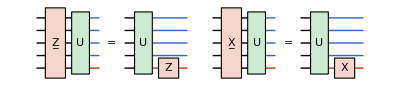

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Translate[{Translate[{Table[Line[{#,y}&/@{-3.5,0}],{y,-2,2}],Table[{If[y==-2,Red,Blue],Line[{{#,y}&/@{0,1.5}}]},{y,-2,2}],opH["Z̲",3.5,{-2,0}],opU["U",3.5,{0,0}]},{-2.5,0}],
Text["="],
Translate[{Table[Line[{#,y}&/@{-1.5,0}],{y,-2,2}],Table[{If[y==-2,Red,Blue],Line[{{#,y}&/@{0,3.5}}]},{y,-2,2}],opH["Z",1,{2,-2}],opU["U",3.5,{0,0}]},{2.5,0}]},{-7,0}],
Translate[{Translate[{Table[Line[{#,y}&/@{-3.5,0}],{y,-2,2}],Table[{If[y==-2,Red,Blue],Line[{{#,y}&/@{0,1.5}}]},{y,-2,2}],opH["X̲",3.5,{-2,0}],opU["U",3.5,{0,0}]},{-2.5,0}],
Text["="],
Translate[{Table[Line[{#,y}&/@{-1.5,0}],{y,-2,2}],Table[{If[y==-2,Red,Blue],Line[{{#,y}&/@{0,3.5}}]},{y,-2,2}],opH["X",1,{2,-2}],opU["U",3.5,{0,0}]},{2.5,0}]},{7,0}]},ImageSize->{Automatic,80}]]
```

Logical gates will not take the system out of the code subspace, as they will not touch the syndrome qubit.

If any of the syndrome qubit is flipped. ⇒ The system is carried out of the code subspace (excitation created). ⇒ Signals an error. ⇒ Correct the error by applying appropriate unitary operations based on the syndrome.

How well is the logical qubit protected? Take the unitary circuit, pin the syndrome qubits and bend around the logical qubit → a six-leg tensor T describing how the logical and the physical qubits are related

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Translate[{Table[Line[{#,y}&/@{-1.5,0}],{y,-2,2}],Table[{Blue,Line[{{#,y}&/@{0,1.5}}]},{y,-1,2}],{Red,BSplineCurve[{{0,-2},{1,-2},{1.5,-2},{1.5,-2.5},{1.5,-3},{1,-3},{0,-3},{-1.5,-3}}]},opU["U",3.5,{0,0}],Text[Style["↑",Blue],{2,#},{-0.5,0.2}]&/@Range[-1,2]},{-4,0}],Text["="],Translate[{Table[Line[{#,y}&/@{-1.5,0}],{y,-2,2}],{Red,Line[{{#,-3}&/@{-1.5,0}}]},opU["T",4,{0,-0.5}]},{2.5,0}]},ImageSize->{Automatic,80}]]
```

-Graphics-

It is a perfect tensor, because of an amazing property: T is proportional to a unitary matrix from any half of legs to the rest half of legs.

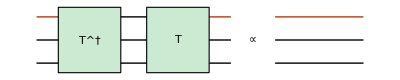

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Rectangle[{-0.8,-n 0.8},{0.8,n 0.8},RoundingRadius->0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,n_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Scale[#,{1,n},{0,0}]&@Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Translate[{Table[Line[{{-1,y},{1,y}}],{y,-0.5,0.5,0.5}],Translate[{Table[{If[y<0.5,Black,Red],Line[{{-1.2,y},{0,y}}]},{y,-0.5,0.5,0.5}],opU["T\^†",1,{0,0}]},{-1,0}],Translate[{Table[{If[y<0.5,Black,Red],Line[{{1.2,y},{0,y}}]},{y,-0.5,0.5,0.5}],opU["T",1,{0,0}]},{1,0}]},{-2.7,0}],
Text["∝"],Translate[Table[{If[y<0.5,Black,Red],Line[{{-1,y},{1,y}}]},{y,-0.5,0.5,0.5}],{1.5,0}]},ImageSize->{Automatic,40}]]
```

```mathematica
Block[{U,T},
U=SparseArray[ⅈ Dot@@
(Represent/@{C4[-σ[2,3,3,1,0]],C4[-σ[0,2,3,3,1]],C4[σ[3,3,1,2,3]],C4[σ[3,3,3,1,2]],C4[σ[3,3,3,3,1]],C4[σ[3,0,3,0,2]],C4[-σ[0,0,0,0,1]],C4[-σ[0,0,0,0,3]]})];
T=ArrayReshape[U.Flatten[{1,0}⊗{1,0}⊗{1,0}⊗{1,0}⊗#],{2,2,2,2,2}]&/@{{1,0},{0,1}};
ArrayRules@tTr[{T,Conjugate[T]},Thread[{#,#+6}&@{1,6,4}]]]
```

{{1,1,1,1,1,1}→1/4,{1,1,2,1,1,2}→1/4,{1,2,1,1,2,1}→1/4,{1,2,2,1,2,2}→1/4,{2,1,1,2,1,1}→1/4,{2,1,2,2,1,2}→1/4,{2,2,1,2,2,1}→1/4,{2,2,2,2,2,2}→1/4,{_,_,_,_,_,_}→0}

Verification.

Treat T as a many-body state (after normalization) ⇒ it describes a pure state of six qubits, where any set of three qubits is maximally entangled with the complementary set of three qubits. Such states have been called absolutely maximally entangled states.

(i) Use the perfect tensor property to show that the nth Rényi entanglement entropy of any m qubits in the six-qubit state T is S^(n)(m)=min(m,6-m)ln 2.
(ii) Use the above result to show Eq. (DisplayFormulaNumbered).

The mutual information between the logical qubit and any m physical qubits is given by

I^(n)(1:m)=Piecewise[{{0, m≤2,}, {2ln 2, m≥3.}}]

The five-qubit code has the property that

any two qubits have no information about the logical qubit.

any three qubits have complete information about the logical qubit.

Therefore the logical qubit is protected against erasure error up to two qubits.